```mathematica
Get["TransportFunctions/IntegrationTables.m"];
```

```mathematica
Get["TransportFunctions/XDataCreation.m"];
```

```mathematica
XDatam55p05=XDataCreation[{-0.055,0.005,0.},32]
```

{-0.055,-0.0530645,-0.051129,-0.0491935,-0.0472581,-0.0453226,-0.0433871,-0.0414516,-0.0395161,-0.0375806,-0.0356452,-0.0337097,-0.0317742,-0.0298387,-0.0279032,-0.0259677,-0.0240323,-0.0220968,-0.0201613,-0.0182258,-0.0162903,-0.0143548,-0.0124194,-0.0104839,-0.00854839,-0.0066129,-0.00467742,-0.00274194,-0.000806452,0.00112903,0.00306452,0.005}

### memoization

```mathematica
ClearAll[FitFuncMemoArith]
```

```mathematica
FitFuncMemoArith[
{b_,alpha_,BRxB_,rRxB_,rD_,rF_,rA_},{xA_,yA_,xOff_,yOff_,y0_},XList_,IntPrec_
]:=
FitFuncMemoArith[{b,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec]=
Reverse[IntegrationTableArith[{b,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec]]
```

### bin selection and normalization

```mathematica
FitFuncBinNormArith[bin_?NumericQ,{b_?NumericQ,alpha_?NumericQ,BRxB_?NumericQ,rRxB_?NumericQ,rD_?NumericQ,rF_?NumericQ,rA_},{xA_,yA_,xOff_,yOff_,y0_},XList_,IntPrec_]:=FitFuncMemoArith[{b,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec][[bin]]/Total[FitFuncMemoArith[{b,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},XList,IntPrec]]
```

# 90° no filter

Data 90° no Filter

```mathematica
t0=AbsoluteTime[];
ILLData90noFilter=Table[{bin,FitFuncBinNormArith[bin,{0.,Pi/2,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam55p05,3]},{bin,1,Length[XDatam55p05]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33401 and 0.00487773 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14544 and 0.00554641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0346 and 0.0089511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4563 and 0.0151011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.027142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8615 and 0.0155816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94809 and 0.00517478 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06116 and 0.036743 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72955 and 0.0121513 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172851 and 0.000378833 for the integral and error estimates.

468.557663

### 450s

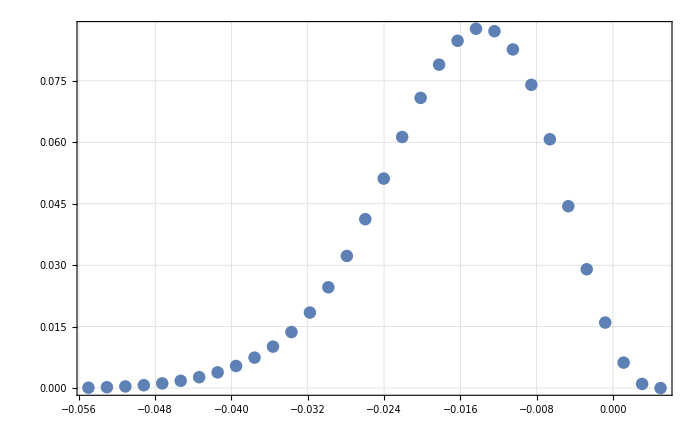

```mathematica
ListPlot[Transpose[{Reverse[XDatam55p05],ILLData90noFilter[[All,2]]}]]
```

```mathematica
(*Export["~/Dropbox/PhD/ElectronTransportSpectrum.txt",Transpose[{Reverse[XDatam55p05],ILLData90noFilter[[All,2]]}],"Table"]*)
```

~/Dropbox/PhD/ElectronTransportSpectrum.txt

Fits

### dB fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
dBFit=Reap[NonlinearModelFit[
ILLData90noFilter,
{
FitFuncBinNormArith[bin,{b,Pi/2,0.2+0.2*5*10^-5,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam55p05,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->6,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Fri 28 Jun 2019 17:40:44

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3336 and 0.00490097 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14497 and 0.00544977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03401 and 0.00901064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.456 and 0.0151044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0272745 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8629 and 0.0156212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1029 and 0.0141341 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3637 and 0.0104337 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94881 and 0.00519046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72997 and 0.0121483 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06158 and 0.0367013 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172883 and 0.000377011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33421 and 0.00490258 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14574 and 0.0054515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0354 and 0.00902454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4574 and 0.0151062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.027273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.0156198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1013 and 0.0141318 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3615 and 0.0104195 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94769 and 0.00525053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72907 and 0.0121454 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06114 and 0.0366921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172789 and 0.000376794 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33425 and 0.0049027 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1458 and 0.00545164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0355 and 0.00902467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4575 and 0.0151064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0272729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8617 and 0.0156197 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1011 and 0.0141316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3613 and 0.0104194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94758 and 0.00525045 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06111 and 0.0366914 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.729 and 0.0121451 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172782 and 0.000376778 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33418 and 0.0049025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14571 and 0.00545142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03533 and 0.00902446 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4574 and 0.0151061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0272731 for the integral and error estimates.

$Aborted

2148.43893

### took 43751s or 12h

```mathematica
dBFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

```mathematica
dBFit[[1]]["BestFitParameters"]
```

{b→0.0001}

### rA fit

```mathematica
t0=AbsoluteTime[];
drAFit=Reap[NonlinearModelFit[
ILLData90noFilter,
{
FitFuncBinNormArith[bin,{b,Pi/2,0.2,1./2,1./2,1.,1/2.+1/2*10^-4},{0.01,0.035,0.,0.,0.},XDatam55p05,3],
-0.003<b<0.003
},
{{b,-0.0001}},bin,MaxIterations->10,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->6,AccuracyGoal->7
]
];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33494 and 0.00491556 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14663 and 0.00554188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0368 and 0.00899804 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4587 and 0.0150685 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4641 and 0.0271248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8607 and 0.0156766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0996 and 0.0141475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3595 and 0.0103893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94614 and 0.00516025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72824 and 0.0121518 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06072 and 0.0367203 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172704 and 0.0003855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33501 and 0.00491574 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14672 and 0.00554208 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03696 and 0.00899823 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4589 and 0.0150687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4641 and 0.0271247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8606 and 0.0156764 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0994 and 0.0141473 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3593 and 0.0103892 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94598 and 0.00516014 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06067 and 0.0367192 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72814 and 0.0121515 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172693 and 0.000385474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33489 and 0.00491544 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14658 and 0.00554175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0367 and 0.00899792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4586 and 0.0150684 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.464 and 0.027125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8608 and 0.0156767 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0997 and 0.0141477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3597 and 0.0103893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94624 and 0.00516032 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06075 and 0.0367209 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7283 and 0.012152 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172711 and 0.000385516 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33419 and 0.00491358 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14568 and 0.00553973 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03511 and 0.00899599 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4569 and 0.015055 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1016 and 0.0141504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3622 and 0.0104251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94788 and 0.00516139 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72935 and 0.0121555 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06126 and 0.0367315 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17282 and 0.000385773 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3349 and 0.00491548 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14659 and 0.00554179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03673 and 0.00899795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4587 and 0.0150684 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.464 and 0.0271249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8608 and 0.0156767 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0997 and 0.0141476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3596 and 0.0103893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94621 and 0.0051603 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72829 and 0.012152 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06075 and 0.0367208 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172709 and 0.000385512 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3332 and 0.00488867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14444 and 0.00543444 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03293 and 0.00899873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4546 and 0.0150521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.026995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8637 and 0.0156778 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1043 and 0.0141541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3657 and 0.0104267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95016 and 0.00516288 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06196 and 0.0367462 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73081 and 0.0121602 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17297 and 0.00038613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33493 and 0.00491554 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14663 and 0.00554186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03678 and 0.00899802 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4587 and 0.0150685 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4641 and 0.0271249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8607 and 0.0156766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0996 and 0.0141475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3596 and 0.0103893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72825 and 0.0121519 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94616 and 0.00516026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06073 and 0.0367204 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172705 and 0.000385503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33355 and 0.00491188 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14487 and 0.00543538 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03369 and 0.00899965 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150531 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8631 and 0.015677 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1034 and 0.0141528 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3645 and 0.0104262 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94937 and 0.00516237 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73031 and 0.0121586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06172 and 0.0367411 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172918 and 0.000386007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33313 and 0.00488849 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14436 and 0.00543424 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03277 and 0.00899854 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4544 and 0.0150519 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0269952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8638 and 0.015678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1045 and 0.0141543 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.366 and 0.0104269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95032 and 0.00516299 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06201 and 0.0367472 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73091 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172981 and 0.000386155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33494 and 0.00491556 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14663 and 0.00554188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0368 and 0.00899804 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4587 and 0.0150685 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4641 and 0.0271248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8607 and 0.0156766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0996 and 0.0141475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3595 and 0.0103893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94614 and 0.00516025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72824 and 0.0121518 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06072 and 0.0367203 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172704 and 0.0003855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3335 and 0.00491175 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14481 and 0.00543524 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03358 and 0.00899952 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4553 and 0.0150529 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8632 and 0.0156771 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1035 and 0.014153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3647 and 0.0104262 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94949 and 0.00516244 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73038 and 0.0121588 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06175 and 0.0367418 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172926 and 0.000386025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33422 and 0.00491365 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14571 and 0.00553981 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03517 and 0.00899606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.457 and 0.0150551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1015 and 0.0141503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3621 and 0.010425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00516135 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72932 and 0.0121553 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06124 and 0.0367311 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172816 and 0.000385764 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33402 and 0.00491312 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14547 and 0.00544018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03474 and 0.00900093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4565 and 0.0150545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271272 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1021 and 0.014151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3628 and 0.0104254 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94828 and 0.00516166 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72961 and 0.0121563 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06138 and 0.0367341 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172846 and 0.000385836 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33487 and 0.00491539 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14655 and 0.00554169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03665 and 0.00899786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4586 and 0.0150683 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.464 and 0.027125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8608 and 0.0156768 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0997 and 0.0141478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3598 and 0.0103894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94629 and 0.00516035 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72834 and 0.0121521 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06077 and 0.0367213 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172714 and 0.000385524 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33457 and 0.00491459 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14617 and 0.00554083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03598 and 0.00899704 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4579 and 0.0150675 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4639 and 0.0271258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8614 and 0.0157275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1006 and 0.0141489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3608 and 0.0104256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94699 and 0.00516081 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72878 and 0.0121536 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06098 and 0.0367258 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17276 and 0.000385633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33325 and 0.00488881 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14451 and 0.00543459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03305 and 0.00899887 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4547 and 0.0150522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0269949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8636 and 0.0156777 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1042 and 0.0141539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3655 and 0.0104266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95003 and 0.0051628 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73073 and 0.01216 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06192 and 0.0367454 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172962 and 0.00038611 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33309 and 0.00488839 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14431 and 0.00543414 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03268 and 0.00899843 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4543 and 0.0150518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0269953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8639 and 0.0156639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1046 and 0.0141545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3661 and 0.0104269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73097 and 0.0121607 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95041 and 0.00516305 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06204 and 0.0367478 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172987 and 0.000386169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33376 and 0.00491244 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14514 and 0.00543597 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03416 and 0.00900023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4559 and 0.0150537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0271278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8628 and 0.0157295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1028 and 0.014152 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3638 and 0.0104258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94888 and 0.00516205 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72999 and 0.0121576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06157 and 0.036738 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172886 and 0.00038593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33424 and 0.00491371 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14574 and 0.00553987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03522 and 0.00899612 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1015 and 0.0141502 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.362 and 0.010425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94777 and 0.00516132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121552 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06122 and 0.0367308 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172812 and 0.000385755 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33367 and 0.0049122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14502 and 0.00543572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03396 and 0.00899998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4557 and 0.0150534 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.027128 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8629 and 0.0157297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1031 and 0.0141523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3641 and 0.010426 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94909 and 0.00516219 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73013 and 0.012158 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06163 and 0.0367393 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.1729 and 0.000385963 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33432 and 0.00491393 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14585 and 0.00554011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03541 and 0.00899635 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0150554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.0157281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1013 and 0.0141499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3617 and 0.0104249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94758 and 0.00516119 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72916 and 0.0121548 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06117 and 0.0367295 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172799 and 0.000385725 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33381 and 0.00491257 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14521 and 0.0054396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03427 and 0.00900036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.456 and 0.0150539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8627 and 0.0157293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1027 and 0.0141518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94877 and 0.00516197 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72992 and 0.0121573 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06153 and 0.0367372 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172878 and 0.000385912 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33309 and 0.00488838 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1443 and 0.00543413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03268 and 0.00899843 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4543 and 0.0150518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0269953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8639 and 0.0156639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1046 and 0.0141545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3661 and 0.0104269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95041 and 0.00516305 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73097 and 0.0121607 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06204 and 0.0367478 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172987 and 0.00038617 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33311 and 0.00488845 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14433 and 0.0054342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03273 and 0.00899849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4544 and 0.0150518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0269952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8639 and 0.0156639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1045 and 0.0141544 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.366 and 0.0104269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95036 and 0.00516301 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73094 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06202 and 0.0367474 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172984 and 0.000386161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33445 and 0.00491426 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14601 and 0.00554047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03569 and 0.00899669 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4576 and 0.0150671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0271261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8616 and 0.0157278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1009 and 0.0141494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3613 and 0.0104246 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94728 and 0.005161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72897 and 0.0121542 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06107 and 0.0367276 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17278 and 0.000385679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33422 and 0.00491365 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14572 and 0.00553981 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03518 and 0.00899607 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.457 and 0.0150551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1015 and 0.0141503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3621 and 0.010425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00516135 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72931 and 0.0121553 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06124 and 0.0367311 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172815 and 0.000385763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33431 and 0.00491389 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14583 and 0.00554007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03537 and 0.00899631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4572 and 0.0150553 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.0157281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1013 and 0.0141499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3618 and 0.0104249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94761 and 0.00516122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72918 and 0.0121549 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06118 and 0.0367298 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172802 and 0.000385731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33374 and 0.00491238 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14511 and 0.00543591 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03411 and 0.00900017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4559 and 0.0150536 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0271279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8628 and 0.0157295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1029 and 0.0141521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3638 and 0.0104258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94893 and 0.00516208 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73003 and 0.0121577 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06158 and 0.0367383 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172889 and 0.000385938 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33414 and 0.00491345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14562 and 0.0055396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.035 and 0.00899586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94799 and 0.00516146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72942 and 0.0121557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0367322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172827 and 0.00038579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33386 and 0.0049127 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14527 and 0.00543973 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03438 and 0.0090005 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.015054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8626 and 0.0157292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1025 and 0.0141516 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3634 and 0.0104256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94865 and 0.0051619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72985 and 0.0121571 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0615 and 0.0367365 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172871 and 0.000385894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33414 and 0.00491345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14562 and 0.0055396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.035 and 0.00899586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94799 and 0.00516146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72942 and 0.0121557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0367322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172827 and 0.00038579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3347 and 0.00491492 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14633 and 0.00554119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03626 and 0.00899738 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4639 and 0.0271254 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8611 and 0.0156772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1002 and 0.0141484 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3604 and 0.0103897 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9467 and 0.00516062 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7286 and 0.012153 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06089 and 0.0367239 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172741 and 0.000385588 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33434 and 0.00491399 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14588 and 0.00554018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03546 and 0.00899641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0150668 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0271263 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.015728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1012 and 0.0141498 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3617 and 0.0104248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94752 and 0.00516116 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72912 and 0.0121547 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06115 and 0.0367292 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172796 and 0.000385717 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33445 and 0.00491426 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14601 and 0.00554047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03569 and 0.00899669 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4576 and 0.0150671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0271261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8616 and 0.0157278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1009 and 0.0141494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3613 and 0.0104246 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94728 and 0.005161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72897 and 0.0121542 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06108 and 0.0367277 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17278 and 0.000385679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33425 and 0.00491373 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14575 and 0.0055399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03524 and 0.00899615 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8619 and 0.0157283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1015 and 0.0141501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.362 and 0.010425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94775 and 0.0051613 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72927 and 0.0121552 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06122 and 0.0367306 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172811 and 0.000385752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33384 and 0.00491265 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14524 and 0.00543968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03434 and 0.00900044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0150539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8626 and 0.0157293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1026 and 0.0141517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3635 and 0.0104257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9487 and 0.00516193 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72988 and 0.0121572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06151 and 0.0367368 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172874 and 0.000385901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33416 and 0.0049135 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14564 and 0.00553965 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03505 and 0.00899591 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4569 and 0.0150549 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3623 and 0.0104251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94795 and 0.00516144 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7294 and 0.0121556 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06128 and 0.0367319 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172824 and 0.000385783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33415 and 0.00491347 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14563 and 0.00553962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03502 and 0.00899588 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150549 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94797 and 0.00516145 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72941 and 0.0121557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0367321 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172826 and 0.000385788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33385 and 0.00491268 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14526 and 0.00543971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03436 and 0.00900047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.015054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8626 and 0.0157292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1026 and 0.0141517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3634 and 0.0104257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94867 and 0.00516191 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72986 and 0.0121571 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0615 and 0.0367366 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172872 and 0.000385897 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33414 and 0.00491345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14562 and 0.0055396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.035 and 0.00899586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94799 and 0.00516146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72942 and 0.0121557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0367322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172827 and 0.00038579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33395 and 0.00491294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14538 and 0.00543999 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03459 and 0.00900075 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4564 and 0.0150543 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271273 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8625 and 0.015729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1023 and 0.0141513 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3631 and 0.0104255 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94844 and 0.00516176 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72971 and 0.0121566 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06143 and 0.0367351 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172857 and 0.000385861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33384 and 0.00491265 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14524 and 0.00543967 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03434 and 0.00900044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0150539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8626 and 0.0157293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1026 and 0.0141517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3635 and 0.0104257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9487 and 0.00516193 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72988 and 0.0121572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06151 and 0.0367368 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172874 and 0.000385902 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33412 and 0.0049134 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1456 and 0.00544047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03496 and 0.0089958 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8622 and 0.0157286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1018 and 0.0141506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3625 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94804 and 0.0051615 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72946 and 0.0121558 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06131 and 0.0367325 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17283 and 0.000385798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33451 and 0.00491442 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14609 and 0.00554064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03583 and 0.00899686 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4577 and 0.0150673 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0271259 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8615 and 0.0157276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1007 and 0.0141492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3611 and 0.0104245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94714 and 0.00516091 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72888 and 0.0121539 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06103 and 0.0367267 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17277 and 0.000385657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33409 and 0.00491331 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14556 and 0.00544038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03488 and 0.00899571 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4567 and 0.0150547 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.027127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8622 and 0.0157286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1019 and 0.0141507 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3626 and 0.0104253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94812 and 0.00516155 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7295 and 0.012156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06133 and 0.036733 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172835 and 0.00038581 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33405 and 0.00491321 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14551 and 0.00544027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03479 and 0.0089956 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0150546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.102 and 0.0141509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3627 and 0.0104253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94821 and 0.00516161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72956 and 0.0121561 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06136 and 0.0367336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172841 and 0.000385824 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33405 and 0.0049132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14551 and 0.00544026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03478 and 0.00899559 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0150546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.102 and 0.0141509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3627 and 0.0104253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94822 and 0.00516161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06136 and 0.0367337 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72957 and 0.0121562 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172842 and 0.000385826 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33414 and 0.00491345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14562 and 0.0055396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.035 and 0.00899586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271268 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94799 and 0.00516146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72942 and 0.0121557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0367322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172827 and 0.00038579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3339 and 0.0049128 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14532 and 0.00543984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03447 and 0.0090006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4562 and 0.0150541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8625 and 0.0157291 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1024 and 0.0141515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3633 and 0.0104256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94857 and 0.00516184 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72979 and 0.0121569 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06147 and 0.0367359 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172865 and 0.000385881 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33388 and 0.00491276 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1453 and 0.0054398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03444 and 0.00900056 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4562 and 0.0150541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8626 and 0.0157292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1025 and 0.0141515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3633 and 0.0104256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9486 and 0.00516186 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72981 and 0.012157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06148 and 0.0367361 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172867 and 0.000385885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33406 and 0.00491324 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14553 and 0.00544031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03483 and 0.00899564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0150546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.027127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.102 and 0.0141508 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3627 and 0.0104253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94818 and 0.00516158 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72954 and 0.0121561 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06135 and 0.0367334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172839 and 0.000385819 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3339 and 0.00491282 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14533 and 0.00543986 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03448 and 0.00900062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4563 and 0.0150541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8625 and 0.0157291 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1024 and 0.0141515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3632 and 0.0104256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94855 and 0.00516183 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06147 and 0.0367358 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72978 and 0.0121569 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172864 and 0.000385878 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33405 and 0.00491321 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14551 and 0.00544027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03479 and 0.0089956 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0150546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.102 and 0.0141509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3627 and 0.0104253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94821 and 0.00516161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72956 and 0.0121561 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06136 and 0.0367336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172841 and 0.000385824 for the integral and error estimates.

22516.43869

### took 22516 s or 6,25h

```mathematica
drAFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0000750132 | 0.0000470927 | 1.59288 | 0.121333

```mathematica
ChiList=Table[{b,
Total[(ILLData90noFilter[[All,2]]-Table[FitFuncBinNormArith[bin,{b,Pi/2,0.2,1./2,1./2,1.,1/2.+1/2*10^-4},{0.01,0.035,0.,0.,0.},XDatam55p05,3],{bin,1,32}])^2]},{b,drAFit[[2,1]]}];
```

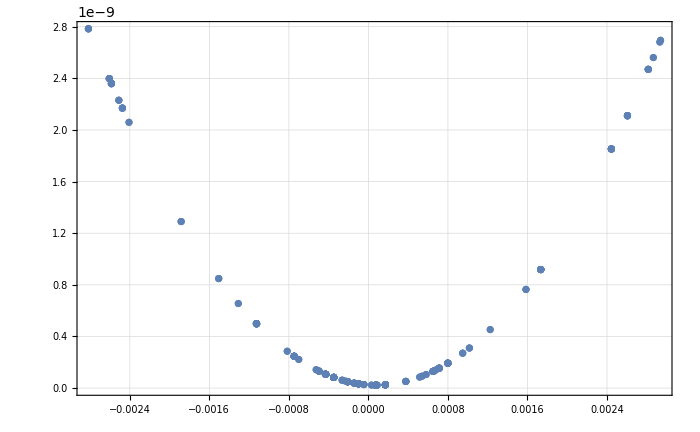

```mathematica
ListPlot[ChiList]
```

```mathematica
drAFit[[1]]["BestFitParameters"][[1,2]]/10^-4
```

0.750132

### Alpha Fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
dAlphaFit=Reap[NonlinearModelFit[
ILLData90noFilter,
{
FitFuncBinNormArith[bin,{b,Pi/2+Pi/2*5*10^-5,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam55p05,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->5,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->6,AccuracyGoal->7
]
];
t1=AbsoluteTime[];
t1-t0
```

Fri 28 Jun 2019 00:27:23

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33444 and 0.00487253 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14592 and 0.00545471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03537 and 0.0089724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0271087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8612 and 0.0154286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3614 and 0.0104483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94748 and 0.00531564 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72909 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0609 and 0.0367961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172799 and 0.000376151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33505 and 0.00487413 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1467 and 0.00545642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03675 and 0.00897407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94604 and 0.00514749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72818 and 0.0121576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06047 and 0.0367869 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172705 and 0.000375935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33509 and 0.00487425 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14676 and 0.00545655 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03685 and 0.0089742 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4584 and 0.015018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271071 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8601 and 0.0154271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3591 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94593 and 0.00514742 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72811 and 0.0121574 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06043 and 0.0367862 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172697 and 0.000375918 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33502 and 0.00487406 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14666 and 0.00545633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03668 and 0.00897399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3594 and 0.010413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94611 and 0.00514754 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72822 and 0.0121578 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06049 and 0.0367874 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172709 and 0.000375945 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33455 and 0.00487282 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14606 and 0.00545501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03562 and 0.0089727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8611 and 0.0154283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3611 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94719 and 0.00514047 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72892 and 0.01216 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06082 and 0.0367944 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172782 and 0.000376112 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33502 and 0.00487408 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14667 and 0.00545636 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0367 and 0.00897401 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.010413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94609 and 0.00514753 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72821 and 0.0121577 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06048 and 0.0367872 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172708 and 0.000375942 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3339 and 0.00487111 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14523 and 0.00545319 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03419 and 0.00896316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4555 and 0.0150364 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8622 and 0.0154298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3634 and 0.0104492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94874 and 0.00531653 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72989 and 0.0121632 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0368042 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172882 and 0.000376344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33504 and 0.00487412 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14669 and 0.0054564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03674 and 0.00897405 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94605 and 0.0051475 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72819 and 0.0121576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06047 and 0.036787 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172705 and 0.000375937 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33412 and 0.0048717 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14552 and 0.00545382 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03466 and 0.00897153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.456 and 0.0150371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4628 and 0.0271095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8618 and 0.0154293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3626 and 0.0104488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94821 and 0.00531616 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72956 and 0.0121621 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06113 and 0.0368008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172847 and 0.000376264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33385 and 0.00487099 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14517 and 0.00545306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03409 and 0.00896304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8623 and 0.0154299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72996 and 0.0121634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94884 and 0.00531661 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06133 and 0.0368049 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172889 and 0.00037636 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33505 and 0.00487413 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1467 and 0.00545642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03675 and 0.00897407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271072 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94604 and 0.00514749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72818 and 0.0121576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06047 and 0.0367869 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172705 and 0.000375935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33406 and 0.00487153 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14543 and 0.00545363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03451 and 0.00897135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4559 and 0.0150369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4628 and 0.0271097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8619 and 0.0154294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3628 and 0.0104489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94837 and 0.00531627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72966 and 0.0121624 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06118 and 0.0368018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172858 and 0.000376287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33457 and 0.00487287 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14609 and 0.00545506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03566 and 0.00897275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271084 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.861 and 0.0154283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.361 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94715 and 0.00514044 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7289 and 0.01216 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06081 and 0.0367942 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172779 and 0.000376106 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33443 and 0.00487252 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14592 and 0.00545469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03536 and 0.00897239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.015038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0271087 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8613 and 0.0154286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3615 and 0.0104483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94749 and 0.00531565 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72909 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06091 and 0.0367961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172799 and 0.000376153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.335 and 0.00487402 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14664 and 0.00545629 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03665 and 0.00897395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4581 and 0.0150178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8603 and 0.0154273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3594 and 0.010413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94614 and 0.00514756 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72824 and 0.0121578 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0605 and 0.0367876 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172711 and 0.00037595 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33482 and 0.00487353 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14641 and 0.00545577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03623 and 0.00897344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4577 and 0.0150172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0271078 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8606 and 0.0154277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3601 and 0.010425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94658 and 0.00514784 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06063 and 0.0367904 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72852 and 0.0121587 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17274 and 0.000376017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33393 and 0.0048712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14528 and 0.00545329 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03427 and 0.00896326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4556 and 0.0150366 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.02711 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8621 and 0.0154297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3633 and 0.0104491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94865 and 0.00531647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72984 and 0.012163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06127 and 0.0368037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172877 and 0.000376331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33383 and 0.00487092 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14514 and 0.00545299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03403 and 0.00896297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4553 and 0.0150362 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271103 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8623 and 0.0154299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9489 and 0.00531665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06134 and 0.0368053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73 and 0.0121636 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172893 and 0.000376369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33424 and 0.00487202 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14567 and 0.00545416 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03493 and 0.00897186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4563 and 0.0150375 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8616 and 0.015429 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3622 and 0.0104486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94793 and 0.00531596 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72938 and 0.0121615 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06104 and 0.036799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172829 and 0.000376221 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33461 and 0.004873 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14615 and 0.0054552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03577 and 0.00897288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4572 and 0.0150386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8609 and 0.0154282 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3608 and 0.010448 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94704 and 0.00514037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72882 and 0.0121597 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06078 and 0.0367934 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172771 and 0.000376089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33474 and 0.00487334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14631 and 0.00545556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03606 and 0.00897324 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4575 and 0.015017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.027108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8607 and 0.0154279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3603 and 0.0104478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94675 and 0.00514795 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72863 and 0.0121591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06068 and 0.0367915 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172751 and 0.000376043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33385 and 0.00487097 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14516 and 0.00545304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03407 and 0.00896302 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271102 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8623 and 0.0154299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94886 and 0.00531662 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72997 and 0.0121635 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06133 and 0.036805 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17289 and 0.000376363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33401 and 0.00487139 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14537 and 0.00545349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03444 and 0.00896346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4557 and 0.0150368 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4628 and 0.0271098 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.862 and 0.0154295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.363 and 0.010449 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94849 and 0.00531635 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72973 and 0.0121627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06121 and 0.0368026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172866 and 0.000376306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33431 and 0.00487219 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14575 and 0.00545434 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03508 and 0.00897204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4565 and 0.0150377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8615 and 0.0154289 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3619 and 0.0104485 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94778 and 0.00531586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.061 and 0.036798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121612 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172819 and 0.000376198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33443 and 0.00487251 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14591 and 0.00545468 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03535 and 0.00897237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.015038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0271088 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8613 and 0.0154286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3615 and 0.0104483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9475 and 0.00531566 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7291 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06091 and 0.0367962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.1728 and 0.000376155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33458 and 0.0048729 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1461 and 0.0054551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03569 and 0.00897278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150385 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.861 and 0.0154283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3609 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94713 and 0.00514043 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0608 and 0.036794 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72888 and 0.0121599 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172777 and 0.000376102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33387 and 0.00487104 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1452 and 0.00545311 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03413 and 0.00896309 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150364 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8622 and 0.0154298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3635 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9488 and 0.00531658 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72994 and 0.0121634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06131 and 0.0368046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172887 and 0.000376354 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33394 and 0.00487121 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14528 and 0.00545329 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03428 and 0.00896326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4556 and 0.0150366 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.02711 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8621 and 0.0154297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3633 and 0.0104491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94865 and 0.00531647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72984 and 0.012163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06127 and 0.0368036 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172877 and 0.000376331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33454 and 0.00487279 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14605 and 0.00545499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0356 and 0.00897267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.457 and 0.0150384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8611 and 0.0154284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3611 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94722 and 0.00514049 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72894 and 0.0121601 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06083 and 0.0367946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172783 and 0.000376116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33417 and 0.00487182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14558 and 0.00545395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03476 and 0.00897166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0150373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8617 and 0.0154292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94811 and 0.00531609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0611 and 0.0368001 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72949 and 0.0121619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17284 and 0.000376247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33474 and 0.00487332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14631 and 0.00545555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03605 and 0.00897322 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4575 and 0.015017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.027108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8607 and 0.0154279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3604 and 0.0104478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94676 and 0.00514796 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72864 and 0.0121591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06069 and 0.0367916 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172752 and 0.000376045 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33432 and 0.00487222 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14577 and 0.00545437 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0351 and 0.00897207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4565 and 0.0150377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.027109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8615 and 0.0154288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3619 and 0.0104485 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94776 and 0.00531584 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72927 and 0.0121612 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06099 and 0.0367979 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172817 and 0.000376194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33417 and 0.00487182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14558 and 0.00545395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03476 and 0.00897166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0150373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271094 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8617 and 0.0154292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94811 and 0.00531609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72949 and 0.0121619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0611 and 0.0368001 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17284 and 0.000376247 for the integral and error estimates.

13770.33362

### took 13770s or 3,8h

```mathematica
dAlphaFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.000916626 | 0.0000928275 | 9.87451 | 4.32917×10^-11

```mathematica
dAlphaFit[[1]]["BestFitParameters"][[1,2]]/(5*10^-5)
```

18.3325

```mathematica
ChiListAlphaFit=Table[{b,
Total[(ILLData90noFilter[[All,2]]-Table[FitFuncBinNormArith[bin,{b,Pi/2+Pi/2*5*10^-5,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam55p05,3],{bin,1,32}])^2]},{b,dAlphaFit[[2,1]]}];
```

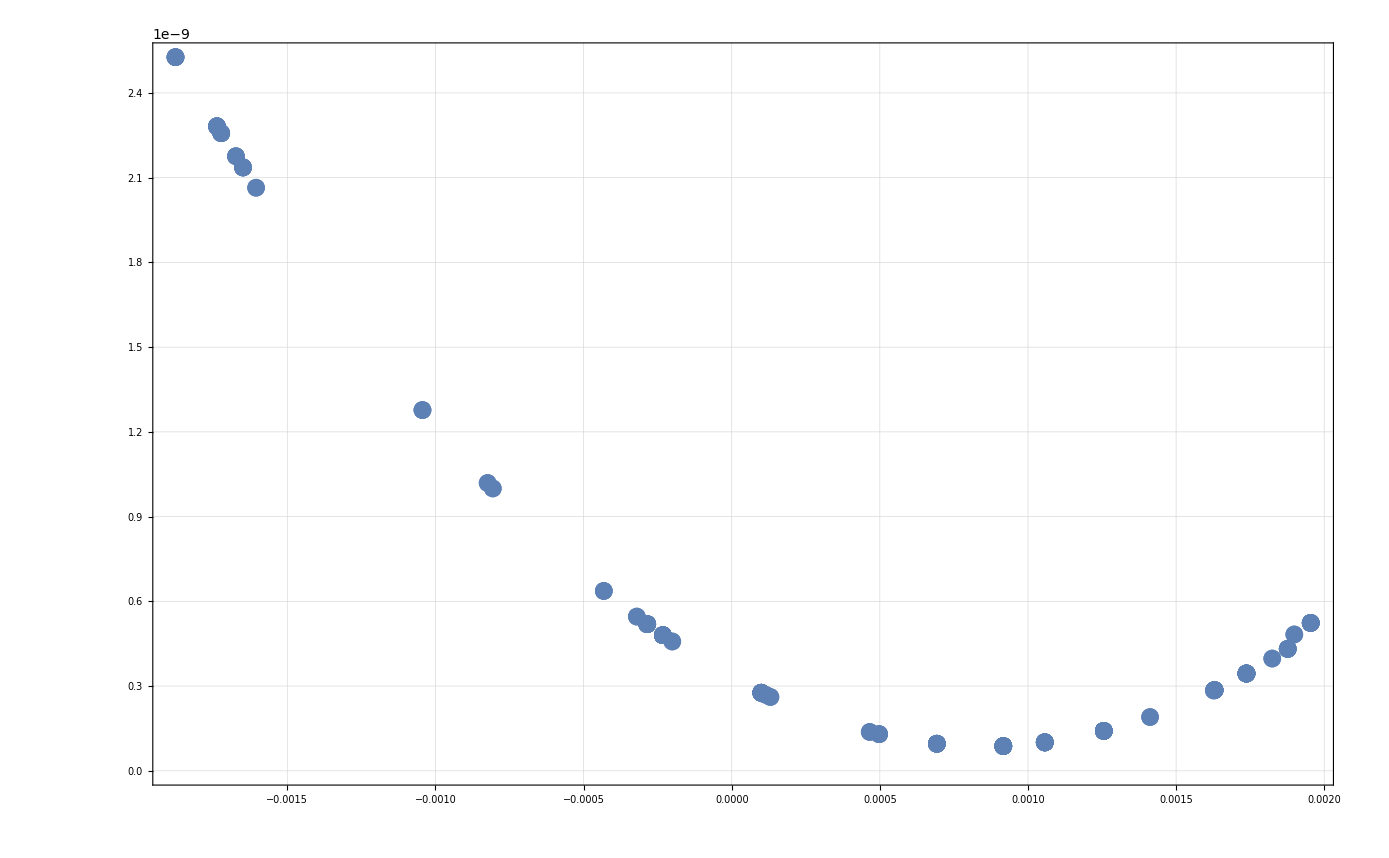

```mathematica
ListPlot[ChiListAlphaFit]
```

```mathematica
dAlphaChiInter=Interpolation[DeleteDuplicatesBy[ChiListAlphaFit,First],InterpolationOrder->2]
```

InterpolatingFunction[{{-0.00187738, 0.00195443}}, <>]

```mathematica
NMinimize[{dAlphaChiInter[x],-0.001<x<0.0015},x]
```

{8.64739×10^-11,{x→0.000860792}}

```mathematica
0.000860792/(5*10^-5)
```

17.2158

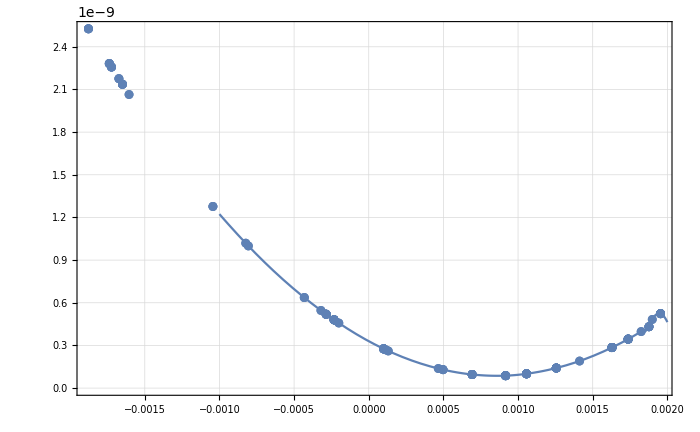

```mathematica
Show[
ListPlot[ChiListAlphaFit],
Plot[dAlphaChiInter[b],{b,-0.001,0.002}]
]
```

# 180° W filter

```mathematica
XDatam85p05=XDataCreation[{-0.085,0.005,0.},32]
```

{-0.085,-0.0820968,-0.0791935,-0.0762903,-0.0733871,-0.0704839,-0.0675806,-0.0646774,-0.0617742,-0.058871,-0.0559677,-0.0530645,-0.0501613,-0.0472581,-0.0443548,-0.0414516,-0.0385484,-0.0356452,-0.0327419,-0.0298387,-0.0269355,-0.0240323,-0.021129,-0.0182258,-0.0153226,-0.0124194,-0.00951613,-0.0066129,-0.00370968,-0.000806452,0.00209677,0.005}

Data

```mathematica
ILLData180WFilter=Import["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ElectronILLData_180°WFilter_Xm85p05_32Bins.txt","Table"]
```

{{0.005,0.},{0.00209677,0.000252048},{-0.000806452,0.0017237},{-0.00370968,0.00539714},{-0.0066129,0.0119853},{-0.00951613,0.0212666},{-0.0124194,0.0323628},{-0.0153226,0.0442408},{-0.0182258,0.0558807},{-0.021129,0.0662973},{-0.0240323,0.0747089},{-0.0269355,0.0804787},{-0.0298387,0.0832502},{-0.0327419,0.0828635},{-0.0356452,0.07949},{-0.0385484,0.0735347},{-0.0414516,0.0655851},{-0.0443548,0.0563155},{-0.0472581,0.046426},{-0.0501613,0.0365969},{-0.0530645,0.0274342},{-0.0559677,0.0195103},{-0.058871,0.0131508},{-0.0617742,0.00849305},{-0.0646774,0.00532177},{-0.0675806,0.00327343},{-0.0704839,0.00195778},{-0.0733871,0.00111995},{-0.0762903,0.000602935},{-0.0791935,0.000298793},{-0.0820968,0.000131299},{-0.085,0.0000498264}}

```mathematica
ILLData180WFilter=Transpose[{Table[i,{i,32}],ILLData180WFilter[[All,2]]}]
```

{{1,0.},{2,0.000252048},{3,0.0017237},{4,0.00539714},{5,0.0119853},{6,0.0212666},{7,0.0323628},{8,0.0442408},{9,0.0558807},{10,0.0662973},{11,0.0747089},{12,0.0804787},{13,0.0832502},{14,0.0828635},{15,0.07949},{16,0.0735347},{17,0.0655851},{18,0.0563155},{19,0.046426},{20,0.0365969},{21,0.0274342},{22,0.0195103},{23,0.0131508},{24,0.00849305},{25,0.00532177},{26,0.00327343},{27,0.00195778},{28,0.00111995},{29,0.000602935},{30,0.000298793},{31,0.000131299},{32,0.0000498264}}

```mathematica
t0=AbsoluteTime[];
ILLData180WFilter=Table[{bin,FitFuncBinNormArith[bin,{0.,Pi,0.2,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDatam85p05,3]},{bin,1,Length[XDatam85p05]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41076 and 0.00245685 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70297 and 0.00306239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95822 and 0.00345261 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.74613 and 0.00340646 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05405 and 0.00242637 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62619 and 0.00177081 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18959 and 0.00138327 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781715 and 0.000953262 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0633593 and 0.0000972753 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926473 and 0.0000314074 for the integral and error estimates.

485.332008

### 450s

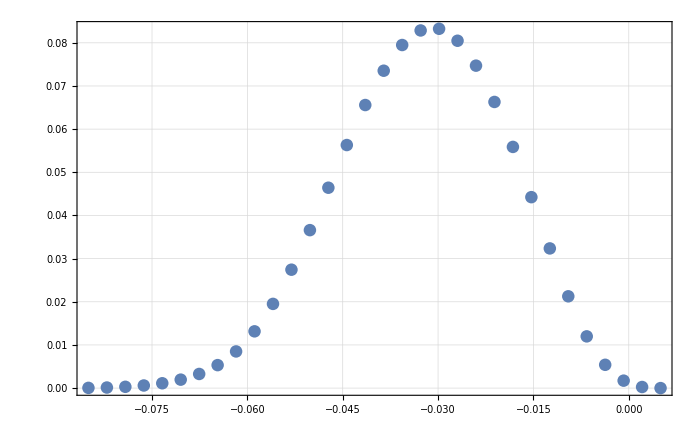

```mathematica
ListPlot[Transpose[{Reverse[XDatam85p05],ILLData180WFilter[[All,2]]}]]
```

```mathematica
(*Export["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ElectronILLData_180°WFilter_Xm85p05_32Bins.txt", Transpose[{Reverse[XDatam85p05],ILLData180WFilter[[All,2]]}],"Table"];*)
```

### intermediate transport with lower alpha

```mathematica
XDatam20p05=XDataCreation[{-0.020,0.005,0.},32]
```

{-0.02,-0.0191935,-0.0183871,-0.0175806,-0.0167742,-0.0159677,-0.0151613,-0.0143548,-0.0135484,-0.0127419,-0.0119355,-0.011129,-0.0103226,-0.00951613,-0.00870968,-0.00790323,-0.00709677,-0.00629032,-0.00548387,-0.00467742,-0.00387097,-0.00306452,-0.00225806,-0.00145161,-0.000645161,0.00016129,0.000967742,0.00177419,0.00258065,0.0033871,0.00419355,0.005}

```mathematica
t0=AbsoluteTime[];
ILLDataBegin180WFilter=Table[{bin,FitFuncBinNormArith[bin,{0.,22.5/180*Pi,0.2,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDatam20p05,3]},{bin,1,Length[XDatam20p05]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0143046 and 0.0000194276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0951694 and 0.000152021 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.13574 and 0.000200873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.262044 and 0.000324667 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.6516 and 0.000676505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.881861 and 0.00168525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.18708 and 0.00179972 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.56615 and 0.00167852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.67259 and 0.00312167 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.24748 and 0.00327098 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.78208 and 0.00335799 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.31509 and 0.00311514 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.890147 and 0.00291334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.552419 and 0.00287134 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.11217 and 0.112134 for the integral and error estimates.

496.902993

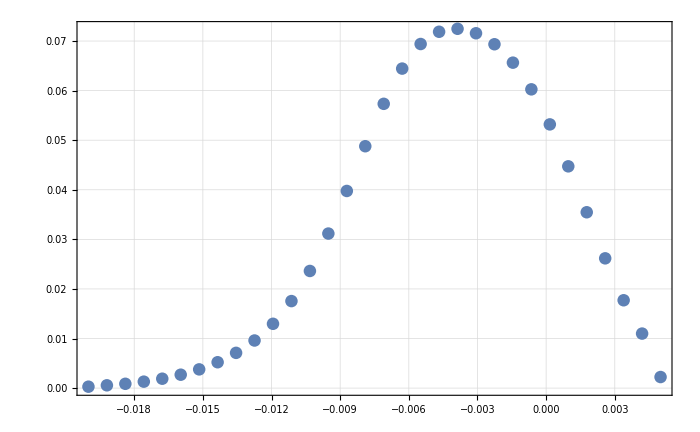

```mathematica
ListPlot[Transpose[{Reverse[XDatam20p05],ILLDataBegin180WFilter[[All,2]]}]]
```

```mathematica
Export["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ElectronILLData_22,5°WFilter_Xm20p05_32Bins.txt",Transpose[{Reverse[XDatam20p05],ILLDataBegin180WFilter[[All,2]]}],"Table"];
```

Fits (still partly only copied from 90° fits)

### dB fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
dBFit=Reap[NonlinearModelFit[
ILLData90noFilter,
{
FitFuncBinNormArith[bin,{b,Pi/2,0.2+0.2*5*10^-5,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam55p05,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->6,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Fri 28 Jun 2019 17:40:44

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3336 and 0.00490097 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14497 and 0.00544977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03401 and 0.00901064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.456 and 0.0151044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0272745 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8629 and 0.0156212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1029 and 0.0141341 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3637 and 0.0104337 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94881 and 0.00519046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72997 and 0.0121483 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06158 and 0.0367013 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172883 and 0.000377011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33421 and 0.00490258 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14574 and 0.0054515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0354 and 0.00902454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4574 and 0.0151062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.027273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.0156198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1013 and 0.0141318 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3615 and 0.0104195 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94769 and 0.00525053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72907 and 0.0121454 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06114 and 0.0366921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172789 and 0.000376794 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33425 and 0.0049027 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1458 and 0.00545164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0355 and 0.00902467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4575 and 0.0151064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0272729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8617 and 0.0156197 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1011 and 0.0141316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3613 and 0.0104194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94758 and 0.00525045 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06111 and 0.0366914 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.729 and 0.0121451 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172782 and 0.000376778 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33418 and 0.0049025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14571 and 0.00545142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03533 and 0.00902446 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4574 and 0.0151061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0272731 for the integral and error estimates.

$Aborted

2148.43893

### took 43751s or 12h

```mathematica
dBFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

```mathematica
dBFit[[1]]["BestFitParameters"]
```

{b→0.0001}

### rA fit

```mathematica
t0=AbsoluteTime[];
drAFit=Reap[NonlinearModelFit[
ILLData180WFilter,
{
FitFuncBinNormArith[bin,{b,Pi,0.2,1.,1.,2.,1.+10^-4},{0.01,0.035,0.,0.,0.},XDatam85p05,3],
-0.003<b<0.003
},
{{b,0.0001}},bin,MaxIterations->10,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->6,AccuracyGoal->7
]
];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41083 and 0.00246741 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70304 and 0.00306209 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95835 and 0.00346338 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74622 and 0.00343003 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0541 and 0.00242463 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62627 and 0.00176986 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18966 and 0.00136572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781753 and 0.000949502 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633637 and 0.0000957935 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926608 and 0.0000310169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41145 and 0.00244613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70359 and 0.00306272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95806 and 0.00346304 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7457 and 0.0034292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05329 and 0.00241975 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62547 and 0.00176354 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18895 and 0.00136487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.78121 and 0.000951346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633073 and 0.0000957119 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00925753 and 0.0000309885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4115 and 0.00244618 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70364 and 0.00306277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95804 and 0.00346301 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74566 and 0.00342913 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05323 and 0.00241967 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.6254 and 0.00176347 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18889 and 0.0013648 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781168 and 0.000951293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633029 and 0.0000957056 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00925687 and 0.0000309863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41142 and 0.00244609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70357 and 0.00306269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95807 and 0.00346306 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74572 and 0.00342924 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05333 and 0.00241981 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62551 and 0.00176359 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18898 and 0.00136491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781237 and 0.000951379 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.06331 and 0.0000957159 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00925795 and 0.0000309899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41094 and 0.00246753 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70313 and 0.00306219 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.9583 and 0.00346332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74614 and 0.00342989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05397 and 0.00242445 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62613 and 0.00176679 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18954 and 0.00136558 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781663 and 0.000949391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633543 and 0.00009578 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926466 and 0.0000310122 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41143 and 0.0024461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70357 and 0.0030627 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95807 and 0.00346305 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74572 and 0.00342923 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05332 and 0.00241979 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62549 and 0.00176357 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18897 and 0.0013649 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781229 and 0.00095137 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633093 and 0.0000957148 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00925783 and 0.0000309895 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41025 and 0.00246677 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70253 and 0.0030615 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95862 and 0.00346369 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74671 and 0.00343079 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05485 and 0.00242181 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.19032 and 0.00136651 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62702 and 0.0017739 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.782254 and 0.000950125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0634157 and 0.0000958688 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00927397 and 0.0000310431 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41145 and 0.00244612 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70359 and 0.00306272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7457 and 0.00342921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95806 and 0.00346304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0533 and 0.00241976 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18895 and 0.00136488 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62547 and 0.00176355 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781214 and 0.000951351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633077 and 0.0000957126 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0092576 and 0.0000309887 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41049 and 0.00246703 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70274 and 0.00306174 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95851 and 0.00346356 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74651 and 0.00343048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05455 and 0.0024252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62671 and 0.00177356 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.19005 and 0.00136619 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.78205 and 0.000949871 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633945 and 0.0000958381 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00927076 and 0.0000310324 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4102 and 0.00246671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70249 and 0.00306145 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95864 and 0.00346371 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74675 and 0.00343086 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05491 and 0.00242189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62708 and 0.00177397 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.19038 and 0.00136658 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.782296 and 0.000950177 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0634201 and 0.0000958751 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00927462 and 0.0000310453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41145 and 0.00244613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70359 and 0.00306272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95806 and 0.00346304 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7457 and 0.0034292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05329 and 0.00241975 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62547 and 0.00176354 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18895 and 0.00136487 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.78121 and 0.000951346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633073 and 0.0000957119 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00925753 and 0.0000309885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41042 and 0.00246696 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70269 and 0.00306168 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95854 and 0.0034636 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74656 and 0.00343057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05463 and 0.00242152 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62679 and 0.00177365 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.19012 and 0.00136628 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.782104 and 0.000949938 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0634001 and 0.0000958462 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0092716 and 0.0000310352 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41095 and 0.00246755 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70315 and 0.00306221 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95829 and 0.00346331 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74612 and 0.00342987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05394 and 0.00242442 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62611 and 0.00176677 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18952 and 0.00136556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781647 and 0.000949371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633527 and 0.0000957776 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926441 and 0.0000310114 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41081 and 0.00246739 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70303 and 0.00306207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95836 and 0.00346339 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74624 and 0.00343005 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05412 and 0.00242466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62629 and 0.00176989 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18968 and 0.00136575 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781767 and 0.00094952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633651 and 0.0000957956 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0092663 and 0.0000310176 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41142 and 0.00246806 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70355 and 0.00306267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95808 and 0.00346306 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74574 and 0.00342926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05335 and 0.00241983 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.189 and 0.00136493 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62553 and 0.00176361 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.78125 and 0.000951396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633114 and 0.0000957179 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00925816 and 0.0000309906 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41122 and 0.00246784 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70338 and 0.00306247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95817 and 0.00346317 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7459 and 0.00342952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05361 and 0.00242016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62578 and 0.0017639 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18922 and 0.0013652 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781422 and 0.000951609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633292 and 0.0000957437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926086 and 0.0000309996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41029 and 0.00246681 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70257 and 0.00306154 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.9586 and 0.00346367 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74668 and 0.00343075 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0548 and 0.00242174 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62697 and 0.00177385 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.19028 and 0.00136646 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.782222 and 0.000950085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0634124 and 0.0000958639 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00927346 and 0.0000310414 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41017 and 0.00246668 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70247 and 0.00306143 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95865 and 0.00346373 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74677 and 0.00343089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05495 and 0.00242193 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62712 and 0.00177401 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.19041 and 0.00136661 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.782319 and 0.000950205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0634225 and 0.0000958785 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00927499 and 0.0000310465 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41062 and 0.00246717 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70285 and 0.00306187 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95845 and 0.00346349 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7464 and 0.00343031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05438 and 0.00242498 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62654 and 0.00177336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1899 and 0.00136601 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781937 and 0.000949731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633828 and 0.0000958212 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926898 and 0.0000310265 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.411 and 0.0024676 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70319 and 0.00306225 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95827 and 0.00346329 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74608 and 0.00342981 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05389 and 0.00242435 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62606 and 0.00176421 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18947 and 0.0013655 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781609 and 0.000949324 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633487 and 0.0000957719 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926381 and 0.0000310094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41057 and 0.00246712 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70281 and 0.00306182 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95847 and 0.00346352 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74644 and 0.00343037 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05444 and 0.00242506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62661 and 0.00177343 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18996 and 0.00136608 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781978 and 0.000949782 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633871 and 0.0000958273 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926962 and 0.0000310287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41097 and 0.00246757 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70317 and 0.00306223 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95828 and 0.0034633 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7461 and 0.00342984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05392 and 0.00242439 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62609 and 0.00176425 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1895 and 0.00136553 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781629 and 0.000949348 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633508 and 0.0000957749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926413 and 0.0000310104 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41069 and 0.00246725 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70291 and 0.00306194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74635 and 0.00343022 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95841 and 0.00346345 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05429 and 0.00242487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18982 and 0.00136592 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62646 and 0.00176846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781878 and 0.000949657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633766 and 0.0000958122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926804 and 0.0000310234 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41017 and 0.00246668 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70247 and 0.00306142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95865 and 0.00346373 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74677 and 0.0034309 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05495 and 0.00242194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62712 and 0.00177401 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.19041 and 0.00136662 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.78232 and 0.000950207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0634226 and 0.0000958788 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00927501 and 0.0000310466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41019 and 0.0024667 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70248 and 0.00306144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95864 and 0.00346372 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74676 and 0.00343087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05493 and 0.00242191 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.6271 and 0.00177399 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.19039 and 0.00136659 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.782306 and 0.000950189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0634211 and 0.0000958766 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00927478 and 0.0000310458 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41112 and 0.00246773 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7033 and 0.00306238 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95821 and 0.00346322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74598 and 0.00342965 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05373 and 0.00242414 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.6259 and 0.00176403 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18933 and 0.00136533 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781502 and 0.000951709 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633376 and 0.0000957558 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926213 and 0.0000310038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4109 and 0.00246749 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7031 and 0.00306216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74616 and 0.00342994 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95832 and 0.00346334 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05401 and 0.00242451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62618 and 0.00176976 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18958 and 0.00136563 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781691 and 0.000949426 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633573 and 0.0000957843 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926511 and 0.0000310137 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41104 and 0.00246764 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70322 and 0.0030623 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95825 and 0.00346327 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74605 and 0.00342975 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05383 and 0.00242428 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62601 and 0.00176415 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18942 and 0.00136544 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781573 and 0.000949279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.063345 and 0.0000957665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926324 and 0.0000310075 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41062 and 0.00246718 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70286 and 0.00306187 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7464 and 0.00343031 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95845 and 0.00346349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05438 and 0.00242498 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62654 and 0.00177336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1899 and 0.00136601 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781936 and 0.00094973 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633827 and 0.000095821 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926896 and 0.0000310265 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41089 and 0.00246747 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70309 and 0.00306214 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95832 and 0.00346335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74618 and 0.00342995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05403 and 0.00242453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.6262 and 0.00176978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1896 and 0.00136565 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781704 and 0.000949441 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633586 and 0.0000957861 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926531 and 0.0000310143 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41075 and 0.00246732 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70297 and 0.003062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95839 and 0.00346342 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74629 and 0.00343014 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05421 and 0.00242477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62638 and 0.00176837 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18975 and 0.00136584 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781824 and 0.00094959 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.063371 and 0.0000958041 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926719 and 0.0000310206 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41089 and 0.00246748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70309 and 0.00306215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74617 and 0.00342995 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95832 and 0.00346335 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05402 and 0.00242453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18959 and 0.00136564 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62619 and 0.00176978 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781701 and 0.000949437 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633582 and 0.0000957857 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926526 and 0.0000310142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41128 and 0.00246791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70343 and 0.00306254 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95814 and 0.00346314 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74585 and 0.00342944 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05353 and 0.00242006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.6257 and 0.00176381 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18915 and 0.00136512 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781368 and 0.000951542 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633237 and 0.0000957356 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926001 and 0.0000309968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41106 and 0.00246766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70324 and 0.00306231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95825 and 0.00346326 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74604 and 0.00342973 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05381 and 0.00242425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62599 and 0.00176413 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18941 and 0.00136542 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.78156 and 0.000949263 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633436 and 0.0000957645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926304 and 0.0000310068 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41105 and 0.00246766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70323 and 0.00306231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95825 and 0.00346326 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74604 and 0.00342974 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05382 and 0.00242426 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62599 and 0.00176413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18941 and 0.00136542 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781563 and 0.000949266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633439 and 0.0000957649 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926308 and 0.0000310069 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41094 and 0.00246753 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70314 and 0.0030622 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.9583 and 0.00346332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74613 and 0.00342989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05396 and 0.00242445 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62612 and 0.00176679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18954 and 0.00136558 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781659 and 0.000949386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633539 and 0.0000957794 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0092646 and 0.000031012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41073 and 0.0024673 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70295 and 0.00306198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.9584 and 0.00346343 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74631 and 0.00343016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05424 and 0.0024248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.6264 and 0.0017684 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18978 and 0.00136586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781842 and 0.000949613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633729 and 0.0000958069 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926748 and 0.0000310215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41091 and 0.0024675 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70311 and 0.00306216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95831 and 0.00346334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74616 and 0.00342993 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.054 and 0.0024245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62617 and 0.00176975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18957 and 0.00136562 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781688 and 0.000949421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633569 and 0.0000957837 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926505 and 0.0000310135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.4109 and 0.00246748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7031 and 0.00306215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95832 and 0.00346334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74617 and 0.00342994 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05402 and 0.00242452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62619 and 0.00176977 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18959 and 0.00136564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781697 and 0.000949433 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633579 and 0.0000957852 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0092652 and 0.000031014 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41074 and 0.00246731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70296 and 0.00306199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95839 and 0.00346343 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7463 and 0.00343015 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05422 and 0.00242478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62639 and 0.00176838 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18976 and 0.00136585 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781832 and 0.000949601 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633719 and 0.0000958054 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926732 and 0.000031021 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41089 and 0.00246748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70309 and 0.00306215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95832 and 0.00346335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74618 and 0.00342995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05403 and 0.00242453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62619 and 0.00176978 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18959 and 0.00136565 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781703 and 0.00094944 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633584 and 0.0000957859 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926529 and 0.0000310143 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41078 and 0.00246736 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.703 and 0.00306204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95837 and 0.0034634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74627 and 0.0034301 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05417 and 0.00242471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62633 and 0.00176832 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18972 and 0.00136579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781796 and 0.000949556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633682 and 0.0000958 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926676 and 0.0000310192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41071 and 0.00246728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70294 and 0.00306197 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.9584 and 0.00346344 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74632 and 0.00343018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05425 and 0.00242482 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18979 and 0.00136588 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62642 and 0.00176842 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781853 and 0.000949627 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633741 and 0.0000958086 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926766 and 0.0000310221 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41085 and 0.00246743 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70306 and 0.00306211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95834 and 0.00346337 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74621 and 0.00343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05408 and 0.00242459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62624 and 0.00176983 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18964 and 0.0013657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781735 and 0.00094948 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633618 and 0.0000957908 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0092658 and 0.000031016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41108 and 0.00246769 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70326 and 0.00306234 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95823 and 0.00346324 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74601 and 0.0034297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05378 and 0.00242421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62595 and 0.00176409 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18937 and 0.00136538 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781536 and 0.000949233 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633412 and 0.0000957609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926267 and 0.0000310056 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41088 and 0.00246746 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70308 and 0.00306213 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95833 and 0.00346335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74618 and 0.00342997 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05404 and 0.00242455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62621 and 0.0017698 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18961 and 0.00136566 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781712 and 0.000949452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633595 and 0.0000957874 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926544 and 0.0000310148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41085 and 0.00246743 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70306 and 0.00306211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95834 and 0.00346337 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74621 and 0.00343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05407 and 0.00242459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62624 and 0.00176983 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18964 and 0.0013657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781735 and 0.00094948 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633618 and 0.0000957908 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926579 and 0.0000310159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41084 and 0.00246742 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70305 and 0.0030621 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95834 and 0.00346337 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74621 and 0.00343001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05409 and 0.00242461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62625 and 0.00176985 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18965 and 0.00136571 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781743 and 0.00094949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633627 and 0.000095792 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926592 and 0.0000310164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41089 and 0.00246747 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70309 and 0.00306214 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95832 and 0.00346335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74618 and 0.00342996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05403 and 0.00242454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1896 and 0.00136565 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.6262 and 0.00176978 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781705 and 0.000949443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633587 and 0.0000957863 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926532 and 0.0000310144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41076 and 0.00246733 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70298 and 0.00306202 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95838 and 0.00346341 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74628 and 0.00343012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05419 and 0.00242474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62636 and 0.00176835 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18974 and 0.00136582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781813 and 0.000949577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633699 and 0.0000958025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926702 and 0.00003102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41077 and 0.00246734 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70298 and 0.00306202 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95838 and 0.00346341 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74628 and 0.00343011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05419 and 0.00242474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62635 and 0.00176835 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18973 and 0.00136581 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781809 and 0.000949572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633695 and 0.0000958019 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926696 and 0.0000310198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41084 and 0.00246742 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70305 and 0.0030621 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95834 and 0.00346337 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74621 and 0.00343001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05409 and 0.00242461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62625 and 0.00176985 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18965 and 0.00136571 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781743 and 0.00094949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633626 and 0.000095792 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926592 and 0.0000310164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41075 and 0.00246732 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70297 and 0.00306201 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95838 and 0.00346342 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74629 and 0.00343013 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0542 and 0.00242476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62637 and 0.00176837 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18975 and 0.00136583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781821 and 0.000949586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633707 and 0.0000958037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00926714 and 0.0000310204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.41085 and 0.00246743 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.70306 and 0.00306211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.95834 and 0.00346337 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74621 and 0.00343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.05408 and 0.00242459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.62624 and 0.00176983 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.18964 and 0.0013657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.781735 and 0.00094948 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0633618 and 0.0000957908 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0092658 and 0.000031016 for the integral and error estimates.

25806.31947

### took 25806 s or 7,2h

```mathematica
drAFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.000011726 | 0.0000119401 | 0.982072 | 0.333667

```mathematica
drAFit[[1]]["BestFitParameters"][[1,2]]/10^-4
```

0.11726

### Alpha Fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
dAlphaFit=Reap[NonlinearModelFit[
ILLData90noFilter,
{
FitFuncBinNormArith[bin,{b,Pi/2+Pi/2*5*10^-5,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam55p05,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->5,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->6,AccuracyGoal->7
]
];
t1=AbsoluteTime[];
t1-t0
```

Fri 28 Jun 2019 00:27:23

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33444 and 0.00487253 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14592 and 0.00545471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03537 and 0.0089724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0271087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8612 and 0.0154286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3614 and 0.0104483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94748 and 0.00531564 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72909 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0609 and 0.0367961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172799 and 0.000376151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33505 and 0.00487413 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1467 and 0.00545642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03675 and 0.00897407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94604 and 0.00514749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72818 and 0.0121576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06047 and 0.0367869 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172705 and 0.000375935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33509 and 0.00487425 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14676 and 0.00545655 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03685 and 0.0089742 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4584 and 0.015018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271071 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8601 and 0.0154271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3591 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94593 and 0.00514742 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72811 and 0.0121574 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06043 and 0.0367862 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172697 and 0.000375918 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33502 and 0.00487406 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14666 and 0.00545633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03668 and 0.00897399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3594 and 0.010413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94611 and 0.00514754 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72822 and 0.0121578 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06049 and 0.0367874 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172709 and 0.000375945 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33455 and 0.00487282 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14606 and 0.00545501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03562 and 0.0089727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8611 and 0.0154283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3611 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94719 and 0.00514047 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72892 and 0.01216 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06082 and 0.0367944 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172782 and 0.000376112 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33502 and 0.00487408 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14667 and 0.00545636 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0367 and 0.00897401 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.010413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94609 and 0.00514753 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72821 and 0.0121577 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06048 and 0.0367872 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172708 and 0.000375942 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3339 and 0.00487111 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14523 and 0.00545319 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03419 and 0.00896316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4555 and 0.0150364 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8622 and 0.0154298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3634 and 0.0104492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94874 and 0.00531653 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72989 and 0.0121632 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0368042 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172882 and 0.000376344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33504 and 0.00487412 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14669 and 0.0054564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03674 and 0.00897405 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94605 and 0.0051475 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72819 and 0.0121576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06047 and 0.036787 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172705 and 0.000375937 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33412 and 0.0048717 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14552 and 0.00545382 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03466 and 0.00897153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.456 and 0.0150371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4628 and 0.0271095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8618 and 0.0154293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3626 and 0.0104488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94821 and 0.00531616 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72956 and 0.0121621 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06113 and 0.0368008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172847 and 0.000376264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33385 and 0.00487099 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14517 and 0.00545306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03409 and 0.00896304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8623 and 0.0154299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72996 and 0.0121634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94884 and 0.00531661 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06133 and 0.0368049 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172889 and 0.00037636 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33505 and 0.00487413 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1467 and 0.00545642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03675 and 0.00897407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271072 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94604 and 0.00514749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72818 and 0.0121576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06047 and 0.0367869 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172705 and 0.000375935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33406 and 0.00487153 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14543 and 0.00545363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03451 and 0.00897135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4559 and 0.0150369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4628 and 0.0271097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8619 and 0.0154294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3628 and 0.0104489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94837 and 0.00531627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72966 and 0.0121624 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06118 and 0.0368018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172858 and 0.000376287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33457 and 0.00487287 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14609 and 0.00545506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03566 and 0.00897275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271084 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.861 and 0.0154283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.361 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94715 and 0.00514044 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7289 and 0.01216 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06081 and 0.0367942 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172779 and 0.000376106 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33443 and 0.00487252 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14592 and 0.00545469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03536 and 0.00897239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.015038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0271087 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8613 and 0.0154286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3615 and 0.0104483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94749 and 0.00531565 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72909 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06091 and 0.0367961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172799 and 0.000376153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.335 and 0.00487402 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14664 and 0.00545629 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03665 and 0.00897395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4581 and 0.0150178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8603 and 0.0154273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3594 and 0.010413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94614 and 0.00514756 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72824 and 0.0121578 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0605 and 0.0367876 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172711 and 0.00037595 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33482 and 0.00487353 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14641 and 0.00545577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03623 and 0.00897344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4577 and 0.0150172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0271078 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8606 and 0.0154277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3601 and 0.010425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94658 and 0.00514784 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06063 and 0.0367904 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72852 and 0.0121587 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17274 and 0.000376017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33393 and 0.0048712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14528 and 0.00545329 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03427 and 0.00896326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4556 and 0.0150366 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.02711 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8621 and 0.0154297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3633 and 0.0104491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94865 and 0.00531647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72984 and 0.012163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06127 and 0.0368037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172877 and 0.000376331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33383 and 0.00487092 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14514 and 0.00545299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03403 and 0.00896297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4553 and 0.0150362 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271103 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8623 and 0.0154299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9489 and 0.00531665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06134 and 0.0368053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73 and 0.0121636 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172893 and 0.000376369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33424 and 0.00487202 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14567 and 0.00545416 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03493 and 0.00897186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4563 and 0.0150375 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8616 and 0.015429 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3622 and 0.0104486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94793 and 0.00531596 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72938 and 0.0121615 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06104 and 0.036799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172829 and 0.000376221 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33461 and 0.004873 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14615 and 0.0054552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03577 and 0.00897288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4572 and 0.0150386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8609 and 0.0154282 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3608 and 0.010448 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94704 and 0.00514037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72882 and 0.0121597 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06078 and 0.0367934 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172771 and 0.000376089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33474 and 0.00487334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14631 and 0.00545556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03606 and 0.00897324 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4575 and 0.015017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.027108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8607 and 0.0154279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3603 and 0.0104478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94675 and 0.00514795 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72863 and 0.0121591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06068 and 0.0367915 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172751 and 0.000376043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33385 and 0.00487097 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14516 and 0.00545304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03407 and 0.00896302 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271102 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8623 and 0.0154299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94886 and 0.00531662 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72997 and 0.0121635 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06133 and 0.036805 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17289 and 0.000376363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33401 and 0.00487139 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14537 and 0.00545349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03444 and 0.00896346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4557 and 0.0150368 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4628 and 0.0271098 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.862 and 0.0154295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.363 and 0.010449 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94849 and 0.00531635 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72973 and 0.0121627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06121 and 0.0368026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172866 and 0.000376306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33431 and 0.00487219 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14575 and 0.00545434 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03508 and 0.00897204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4565 and 0.0150377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8615 and 0.0154289 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3619 and 0.0104485 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94778 and 0.00531586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.061 and 0.036798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121612 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172819 and 0.000376198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33443 and 0.00487251 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14591 and 0.00545468 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03535 and 0.00897237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.015038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0271088 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8613 and 0.0154286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3615 and 0.0104483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9475 and 0.00531566 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7291 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06091 and 0.0367962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.1728 and 0.000376155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33458 and 0.0048729 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1461 and 0.0054551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03569 and 0.00897278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150385 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.861 and 0.0154283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3609 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94713 and 0.00514043 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0608 and 0.036794 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72888 and 0.0121599 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172777 and 0.000376102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33387 and 0.00487104 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1452 and 0.00545311 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03413 and 0.00896309 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150364 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8622 and 0.0154298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3635 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9488 and 0.00531658 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72994 and 0.0121634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06131 and 0.0368046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172887 and 0.000376354 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33394 and 0.00487121 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14528 and 0.00545329 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03428 and 0.00896326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4556 and 0.0150366 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.02711 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8621 and 0.0154297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3633 and 0.0104491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94865 and 0.00531647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72984 and 0.012163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06127 and 0.0368036 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172877 and 0.000376331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33454 and 0.00487279 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14605 and 0.00545499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0356 and 0.00897267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.457 and 0.0150384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8611 and 0.0154284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3611 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94722 and 0.00514049 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72894 and 0.0121601 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06083 and 0.0367946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172783 and 0.000376116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33417 and 0.00487182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14558 and 0.00545395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03476 and 0.00897166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0150373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8617 and 0.0154292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94811 and 0.00531609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0611 and 0.0368001 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72949 and 0.0121619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17284 and 0.000376247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33474 and 0.00487332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14631 and 0.00545555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03605 and 0.00897322 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4575 and 0.015017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.027108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8607 and 0.0154279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3604 and 0.0104478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94676 and 0.00514796 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72864 and 0.0121591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06069 and 0.0367916 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172752 and 0.000376045 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33432 and 0.00487222 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14577 and 0.00545437 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0351 and 0.00897207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4565 and 0.0150377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.027109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8615 and 0.0154288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3619 and 0.0104485 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94776 and 0.00531584 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72927 and 0.0121612 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06099 and 0.0367979 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172817 and 0.000376194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33417 and 0.00487182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14558 and 0.00545395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03476 and 0.00897166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0150373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271094 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8617 and 0.0154292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94811 and 0.00531609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72949 and 0.0121619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0611 and 0.0368001 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17284 and 0.000376247 for the integral and error estimates.

13770.33362

### took 13770s or 3,8h

```mathematica
dAlphaFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.000916626 | 0.0000928275 | 9.87451 | 4.32917×10^-11

```mathematica
dAlphaFit[[1]]["BestFitParameters"][[1,2]]/(5*10^-5)
```

18.3325

```mathematica
ChiListAlphaFit=Table[{b,
Total[(ILLData90noFilter[[All,2]]-Table[FitFuncBinNormArith[bin,{b,Pi/2+Pi/2*5*10^-5,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam55p05,3],{bin,1,32}])^2]},{b,dAlphaFit[[2,1]]}];
```

```mathematica
ListPlot[ChiListAlphaFit]
```

-Graphics-

```mathematica
dAlphaChiInter=Interpolation[DeleteDuplicatesBy[ChiListAlphaFit,First],InterpolationOrder->2]
```

InterpolatingFunction[{{-0.00187738, 0.00195443}}, <>]

```mathematica
NMinimize[{dAlphaChiInter[x],-0.001<x<0.0015},x]
```

{8.64739×10^-11,{x→0.000860792}}

```mathematica
0.000860792/(5*10^-5)
```

17.2158

```mathematica
Show[
ListPlot[ChiListAlphaFit],
Plot[dAlphaChiInter[b],{b,-0.001,0.002}]
]
```

-Graphics-

# 180° at PERC

```mathematica
XDatam70p05=XDataCreation[{-0.070,0.005,0.},32]
```

{-0.07,-0.0675806,-0.0651613,-0.0627419,-0.0603226,-0.0579032,-0.0554839,-0.0530645,-0.0506452,-0.0482258,-0.0458065,-0.0433871,-0.0409677,-0.0385484,-0.036129,-0.0337097,-0.0312903,-0.028871,-0.0264516,-0.0240323,-0.0216129,-0.0191935,-0.0167742,-0.0143548,-0.0119355,-0.00951613,-0.00709677,-0.00467742,-0.00225806,0.00016129,0.00258065,0.005}

### Data (BDV = 1.5T)

```mathematica
t0=AbsoluteTime[];
PERCData180=Table[{bin,FitFuncBinNormArith[bin,{0.,Pi,0.2,0.2/1.5,0.2/1.5,4.,0.2/1.5},{0.01,0.035,0.,0.,0.},XDatam70p05,3]},{bin,1,Length[XDatam70p05]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74406 and 0.00275347 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34389 and 0.00243879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10046 and 0.00217815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901291 and 0.00111872 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481701 and 0.00161171 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938561 and 0.000100574 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299955 and 0.0000449281 for the integral and error estimates.

470.017208

### took 470s

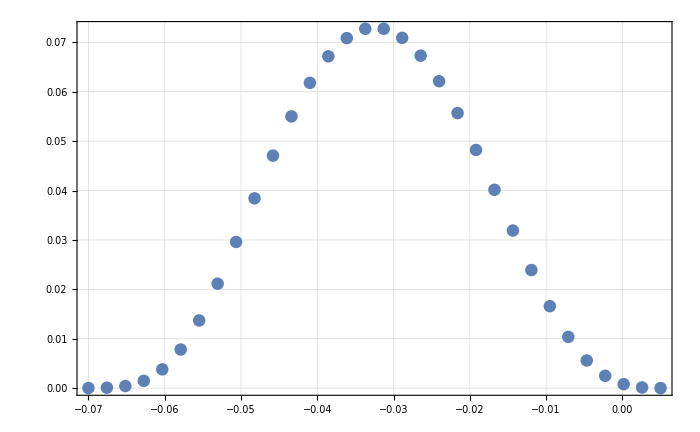

```mathematica
ListPlot[Transpose[{Reverse[XDatam70p05],PERCData180[[All,2]]}]]
```

```mathematica
t0=AbsoluteTime[];
PERCData180b1em3=Table[{bin,FitFuncBinNormArith[bin,{1.*10^-3,Pi,0.2,0.2/1.5,0.2/1.5,4.,0.2/1.5},{0.01,0.035,0.,0.,0.},XDatam70p05,3]},{bin,1,Length[XDatam70p05]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74404 and 0.00275347 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34409 and 0.00243898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10071 and 0.00217841 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901508 and 0.00112012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481866 and 0.00161226 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938864 and 0.000100605 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300055 and 0.0000449429 for the integral and error estimates.

466.457733

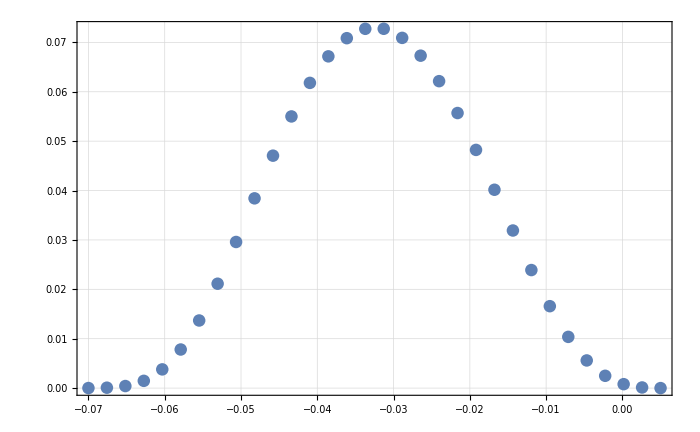

```mathematica
ListPlot[Transpose[{Reverse[XDatam70p05],PERCData180b1em3[[All,2]]}]]
```

```mathematica
(*Export["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ElectronPERCData_180°_Xm70p05_32Bins.txt",Transpose[{Reverse[XDatam70p05],PERCData180[[All,2]]}],"Table"];
Export["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/ElectronPERCData_180°_Xm70p05_32Bins_b1e-3.txt",Transpose[{Reverse[XDatam70p05],PERCData180b1em3[[All,2]]}],"Table"];*)
```

Fits

### dB fit

```mathematica
CloseKernels[];
LaunchKernels[2];
```

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
dBFitPERC=Reap[NonlinearModelFit[
PERCData180,
{
FitFuncBinNormArith[bin,{b,Pi,0.2+0.2*5*10^-5,0.2/1.5,0.2/1.5,4.,0.2/1.5},{0.01,0.035,0.,0.,0.},XDatam70p05,3],
-0.002<b<0.002
},
{{b,-0.0005}},bin,MaxIterations->6,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Mon 4 Nov 2019 10:51:56

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74427 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34406 and 0.0024458 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10059 and 0.0021849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901293 and 0.00110823 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938557 and 0.000101313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299952 and 0.0000449492 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481679 and 0.00161158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74431 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34382 and 0.00244556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10029 and 0.00218457 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901021 and 0.00111477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.093818 and 0.000101274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299827 and 0.0000449308 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481475 and 0.00161089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74432 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34379 and 0.00244553 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10025 and 0.00218453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.900991 and 0.00111474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938138 and 0.000101269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299813 and 0.0000449287 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481452 and 0.00161082 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74431 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34383 and 0.00244558 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10031 and 0.00218459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.90104 and 0.00111345 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938207 and 0.000101276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299836 and 0.0000449321 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481489 and 0.00161094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34411 and 0.00244585 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10065 and 0.00218497 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901351 and 0.0011083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938638 and 0.000101321 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299978 and 0.0000449531 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481723 and 0.00161173 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74431 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34383 and 0.00244557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.1003 and 0.00218458 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901035 and 0.00111344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.09382 and 0.000101276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299834 and 0.0000449318 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481485 and 0.00161093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74423 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34449 and 0.00244624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10113 and 0.00218625 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901776 and 0.00110817 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0939235 and 0.000101383 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300176 and 0.0000449823 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00482047 and 0.00161281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74431 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34382 and 0.00244556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10029 and 0.00218457 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901024 and 0.00111478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938185 and 0.000101274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299829 and 0.000044931 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481477 and 0.0016109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74424 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34436 and 0.00244611 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10096 and 0.00218607 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901631 and 0.00110815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0939029 and 0.000101362 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300108 and 0.0000449722 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481936 and 0.00161244 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74423 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34452 and 0.00244627 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10116 and 0.00218629 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901806 and 0.00110821 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0939277 and 0.000101388 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.030019 and 0.0000449843 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0048207 and 0.00161289 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74431 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34382 and 0.00244556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10029 and 0.00218457 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901021 and 0.00111477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.093818 and 0.000101274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299827 and 0.0000449308 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481475 and 0.00161089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74425 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34433 and 0.00244608 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10092 and 0.00218602 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901596 and 0.00110811 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.093898 and 0.000101357 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300092 and 0.0000449698 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481909 and 0.00161235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.3441 and 0.00244584 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10064 and 0.00218496 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.90134 and 0.00110828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938622 and 0.000101319 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299973 and 0.0000449524 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481715 and 0.0016117 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34418 and 0.00244592 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10074 and 0.00218506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901426 and 0.00110676 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938743 and 0.000101332 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300013 and 0.0000449583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0048178 and 0.00161192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74431 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34384 and 0.00244559 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10032 and 0.0021846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.90105 and 0.00111346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.093822 and 0.000101278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.029984 and 0.0000449328 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481497 and 0.00161097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74432 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34378 and 0.00244552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10024 and 0.00218452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.900982 and 0.00111473 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938125 and 0.000101268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299809 and 0.0000449281 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481445 and 0.00161079 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34415 and 0.0024459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.1007 and 0.00218503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901396 and 0.00110673 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938701 and 0.000101328 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299999 and 0.0000449562 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481757 and 0.00161184 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74423 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34448 and 0.00244622 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10111 and 0.00218623 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.90176 and 0.00110927 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0939211 and 0.000101381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300168 and 0.0000449811 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00482034 and 0.00161277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74431 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34386 and 0.00244561 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10035 and 0.00218463 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901075 and 0.00111349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938256 and 0.000101282 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299852 and 0.0000449345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481516 and 0.00161103 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74423 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34454 and 0.00244628 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10118 and 0.00218631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901823 and 0.00110823 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0939301 and 0.00010139 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300198 and 0.0000449855 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00482083 and 0.00161293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74431 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34392 and 0.00244567 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10042 and 0.00218471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.90114 and 0.00111212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938348 and 0.000101291 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299882 and 0.000044939 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481566 and 0.0016112 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34414 and 0.00244589 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10069 and 0.00218501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901385 and 0.00110671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938687 and 0.000101326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299995 and 0.0000449555 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0048175 and 0.00161181 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74425 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34432 and 0.00244606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10091 and 0.00218525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901579 and 0.00110809 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938956 and 0.000101354 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300084 and 0.0000449687 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481896 and 0.0016123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74427 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34406 and 0.0024458 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10059 and 0.0021849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901295 and 0.00110823 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938559 and 0.000101313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299952 and 0.0000449493 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481681 and 0.00161158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.3441 and 0.00244584 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10064 and 0.00218495 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901337 and 0.00110828 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938618 and 0.000101319 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299972 and 0.0000449522 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481712 and 0.00161169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74431 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34393 and 0.00244568 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10043 and 0.00218473 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901153 and 0.00111093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938361 and 0.000101292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299887 and 0.0000449396 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481573 and 0.00161122 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74427 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34409 and 0.00244583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10062 and 0.00218494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901326 and 0.00110827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938602 and 0.000101317 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299967 and 0.0000449514 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481704 and 0.00161166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34414 and 0.00244588 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10068 and 0.002185 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901378 and 0.00110671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938677 and 0.000101325 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299991 and 0.000044955 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481744 and 0.0016118 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74431 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34382 and 0.00244557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.1003 and 0.00218458 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901031 and 0.00111479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938194 and 0.000101275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299831 and 0.0000449315 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481482 and 0.00161092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.3441 and 0.00244584 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10064 and 0.00218496 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.90134 and 0.00110829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938622 and 0.00010132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299973 and 0.0000449524 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481715 and 0.0016117 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74432 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34379 and 0.00244554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10026 and 0.00218453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.900995 and 0.00111474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938143 and 0.00010127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299815 and 0.000044929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481455 and 0.00161083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74427 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34401 and 0.00244576 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10053 and 0.00218484 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901244 and 0.00110817 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938488 and 0.000101306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299929 and 0.0000449458 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481642 and 0.00161145 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74431 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.3439 and 0.00244565 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.1004 and 0.00218469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901118 and 0.00111354 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938316 and 0.000101288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299872 and 0.0000449375 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481549 and 0.00161114 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74427 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.344 and 0.00244574 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10052 and 0.00218482 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901228 and 0.00110968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938465 and 0.000101303 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299921 and 0.0000449447 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481629 and 0.00161141 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.7443 and 0.00276752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34395 and 0.0024457 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10046 and 0.00218476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901181 and 0.00111072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938396 and 0.000101296 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299899 and 0.0000449414 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481592 and 0.00161129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34421 and 0.00244595 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10077 and 0.0021851 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901456 and 0.0011068 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938786 and 0.000101337 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300028 and 0.0000449604 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481804 and 0.00161199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34418 and 0.00244592 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10074 and 0.00218507 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901428 and 0.00110676 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938746 and 0.000101332 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300014 and 0.0000449584 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481782 and 0.00161192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34415 and 0.0024459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10071 and 0.00218503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901399 and 0.00110673 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938706 and 0.000101328 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300001 and 0.0000449565 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0048176 and 0.00161185 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74426 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34417 and 0.00244591 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10072 and 0.00218505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901412 and 0.00110674 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938724 and 0.00010133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0300007 and 0.0000449573 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0048177 and 0.00161188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.74427 and 0.0027548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.34401 and 0.00244576 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.10053 and 0.00218484 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.901244 and 0.00110817 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0938488 and 0.000101306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0299929 and 0.0000449458 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00481642 and 0.00161145 for the integral and error estimates.

37343.677118

### took 37343s or 10.4h - 2 cores

```mathematica
dBFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | -0.00088704 | 0.000129976 | -6.82464 | 1.20369×10^-7

```mathematica
dBFit[[1]]["BestFitParameters"][[1,2]]/(5*10^-5)
```

-17.7408

### rA fit

```mathematica
CloseKernels[]
```

{KernelObject[5,local,<defunct>],KernelObject[6,local,<defunct>]}

```mathematica
LaunchKernels[3]
```

{KernelObject[7,local],KernelObject[8,local],KernelObject[9,local]}

```mathematica
t0=AbsoluteTime[];
drAFitPERC=Reap[NonlinearModelFit[
PERCData180,
{
FitFuncBinNormArith[bin,{b,Pi,0.2,0.2/1.5,0.2/1.5,4.,0.2/1.5+0.2/1.5*10^-4},{0.01,0.035,0.,0.,0.},XDatam70p05,3],
-0.002<b<0.002
},
{{b,0.0005}},bin,MaxIterations->10,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->6,AccuracyGoal->7
]
];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54878 and 0.0026286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23336 and 0.00234419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00138 and 0.00224262 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858888 and 0.00104009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466486 and 0.00158777 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894466 and 0.000100992 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285835 and 0.0000461179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54865 and 0.00262845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23294 and 0.00234374 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00087 and 0.00223229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858424 and 0.00103952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466129 and 0.00158655 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0893818 and 0.000100921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285621 and 0.0000460839 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54864 and 0.00262844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23291 and 0.00234371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00083 and 0.00223225 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858395 and 0.00103949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466106 and 0.00158648 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0893777 and 0.000100917 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285607 and 0.0000460818 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54866 and 0.00262846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23295 and 0.00234376 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00089 and 0.00223232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858443 and 0.00103954 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466143 and 0.0015866 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0893844 and 0.000100924 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285629 and 0.0000460853 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54874 and 0.00262855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23322 and 0.00234404 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00121 and 0.0022327 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858738 and 0.00103985 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466369 and 0.00158737 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894254 and 0.000100969 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285765 and 0.0000461068 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54865 and 0.00262846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23295 and 0.00234375 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00088 and 0.00223231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858438 and 0.00103953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466139 and 0.00158659 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0893837 and 0.000100923 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285627 and 0.0000460849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54885 and 0.00262869 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23359 and 0.00234443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00166 and 0.00223815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859143 and 0.0010441 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466683 and 0.00158844 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894823 and 0.000101031 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285953 and 0.0000461366 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54865 and 0.00262845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23294 and 0.00234374 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00087 and 0.0022323 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858427 and 0.00103952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466131 and 0.00158656 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0893822 and 0.000100922 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285622 and 0.0000460842 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54881 and 0.00262864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23346 and 0.0023443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00151 and 0.00224277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859004 and 0.00104122 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466575 and 0.00158807 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894627 and 0.00010101 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285888 and 0.0000461263 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54886 and 0.0026287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23361 and 0.00234446 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00169 and 0.00223819 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859171 and 0.00104414 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466705 and 0.00158852 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894863 and 0.000101036 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285967 and 0.0000461387 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54865 and 0.00262845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23294 and 0.00234374 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00087 and 0.00223229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858424 and 0.00103952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466129 and 0.00158655 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0893818 and 0.000100921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285621 and 0.0000460839 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54884 and 0.00262867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23354 and 0.00234438 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00161 and 0.00224289 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859095 and 0.00104544 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466645 and 0.00158831 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894753 and 0.000101024 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.028593 and 0.000046133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54873 and 0.00262855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23321 and 0.00234403 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0012 and 0.00223269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858727 and 0.00103984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466361 and 0.00158734 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894239 and 0.000100967 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.028576 and 0.000046106 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54876 and 0.00262858 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23328 and 0.00234411 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00129 and 0.00223279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858808 and 0.00104 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466424 and 0.00158756 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894354 and 0.00010098 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285798 and 0.000046112 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54866 and 0.00262846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23296 and 0.00234377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0009 and 0.00223233 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858452 and 0.00103955 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0046615 and 0.00158663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0893856 and 0.000100926 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285633 and 0.0000460859 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54869 and 0.00262849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23305 and 0.00234386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.001 and 0.00223245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858551 and 0.00103963 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466224 and 0.00158688 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0893991 and 0.00010094 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285678 and 0.000046093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54884 and 0.00262868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23357 and 0.00234441 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00164 and 0.00224293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85912 and 0.00104408 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466666 and 0.00158838 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894792 and 0.000101028 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285943 and 0.000046135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54886 and 0.0026287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23363 and 0.00234448 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00171 and 0.00223821 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859187 and 0.00104415 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466717 and 0.00158856 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894886 and 0.000101038 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285974 and 0.0000461399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.5488 and 0.00262863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23342 and 0.00234425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00146 and 0.00224271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858959 and 0.00104116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466539 and 0.00158795 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894563 and 0.000101003 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285867 and 0.000046123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54871 and 0.00262852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23314 and 0.00234395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00111 and 0.00223258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858648 and 0.00103974 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466299 and 0.00158713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894127 and 0.000100955 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285723 and 0.0000461001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.5487 and 0.00262851 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23311 and 0.00234392 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00108 and 0.00223254 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858616 and 0.00103971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466275 and 0.00158705 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894083 and 0.00010095 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285708 and 0.0000460978 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54885 and 0.00262868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23357 and 0.00234441 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00164 and 0.00223813 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859125 and 0.00104408 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466669 and 0.00158839 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894799 and 0.000101028 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285945 and 0.0000461353 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54866 and 0.00262846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23297 and 0.00234377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0009 and 0.00223234 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858458 and 0.00103956 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466154 and 0.00158664 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0893865 and 0.000100927 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285636 and 0.0000460864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54884 and 0.00262868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23357 and 0.00234441 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00164 and 0.00224293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859121 and 0.00104408 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466666 and 0.00158838 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894792 and 0.000101028 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285943 and 0.000046135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54871 and 0.00262852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23313 and 0.00234395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00111 and 0.00223258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858645 and 0.00103974 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466297 and 0.00158713 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894123 and 0.000100955 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285722 and 0.0000460999 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54882 and 0.00262865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23348 and 0.00234432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00154 and 0.0022428 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859029 and 0.00104124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466594 and 0.00158814 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894661 and 0.000101013 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.02859 and 0.0000461281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54865 and 0.00262845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23294 and 0.00234374 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00086 and 0.00223229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858421 and 0.00103952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466126 and 0.00158654 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0893813 and 0.000100921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285619 and 0.0000460837 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54872 and 0.00262854 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23318 and 0.00234399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00116 and 0.00223264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85869 and 0.00103979 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466332 and 0.00158725 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894187 and 0.000100962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285743 and 0.0000461033 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54886 and 0.0026287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.2336 and 0.00234445 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00168 and 0.00223818 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85916 and 0.00104412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466697 and 0.00158849 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894848 and 0.000101034 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285962 and 0.0000461379 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54884 and 0.00262868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23357 and 0.00234441 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00164 and 0.00224293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85912 and 0.00104408 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466665 and 0.00158838 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894791 and 0.000101028 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285943 and 0.000046135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54874 and 0.00262856 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23323 and 0.00234405 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00122 and 0.00223271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858745 and 0.00103985 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466374 and 0.00158739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894263 and 0.00010097 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285768 and 0.0000461073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54881 and 0.00262865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23347 and 0.00234431 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00152 and 0.00224279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859015 and 0.00104123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466583 and 0.0015881 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894642 and 0.000101011 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285893 and 0.0000461271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54876 and 0.00262858 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23328 and 0.00234411 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00129 and 0.00223279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858808 and 0.00104 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466424 and 0.00158756 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894354 and 0.00010098 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285798 and 0.000046112 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54871 and 0.00262852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23313 and 0.00234395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00111 and 0.00223257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858641 and 0.00103974 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466294 and 0.00158712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894118 and 0.000100954 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.028572 and 0.0000460996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54878 and 0.00262861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23336 and 0.00234419 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00138 and 0.00224262 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858892 and 0.00104109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466488 and 0.00158778 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894469 and 0.000100993 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285836 and 0.0000461181 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54885 and 0.00262869 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.2336 and 0.00234444 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00168 and 0.00223817 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859155 and 0.00104412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466693 and 0.00158847 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894841 and 0.000101033 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285959 and 0.0000461375 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54881 and 0.00262864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23345 and 0.00234428 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00149 and 0.00224275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85899 and 0.0010412 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466563 and 0.00158803 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894606 and 0.000101007 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285881 and 0.0000461252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54873 and 0.00262855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23321 and 0.00234403 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0012 and 0.00223269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858728 and 0.00103984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466361 and 0.00158734 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.089424 and 0.000100967 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.028576 and 0.000046106 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54873 and 0.00262854 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23319 and 0.00234401 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00118 and 0.00223266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858704 and 0.00103981 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466342 and 0.00158728 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894206 and 0.000100964 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285749 and 0.0000461043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54878 and 0.0026286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23334 and 0.00234417 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00137 and 0.0022426 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858875 and 0.00104008 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466476 and 0.00158774 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894448 and 0.00010099 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285829 and 0.0000461169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54883 and 0.00262867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23352 and 0.00234436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00159 and 0.00224286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859074 and 0.00104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466628 and 0.00158825 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894724 and 0.00010102 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285921 and 0.0000461314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54885 and 0.00262869 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23359 and 0.00234444 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00167 and 0.00223816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859148 and 0.00104411 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466687 and 0.00158845 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.089483 and 0.000101032 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285956 and 0.000046137 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54881 and 0.00262864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23346 and 0.0023443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00151 and 0.00224278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859009 and 0.00104122 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466578 and 0.00158808 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894633 and 0.00010101 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.028589 and 0.0000461266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54882 and 0.00262865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23349 and 0.00234433 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00154 and 0.00224281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859035 and 0.00104125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466599 and 0.00158815 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.089467 and 0.000101014 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285903 and 0.0000461286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54881 and 0.00262865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23347 and 0.00234431 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00152 and 0.00224278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859014 and 0.00104123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466582 and 0.0015881 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.089464 and 0.000101011 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285893 and 0.000046127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54881 and 0.00262865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23347 and 0.0023443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00152 and 0.00224278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859013 and 0.00104122 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466581 and 0.00158809 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894638 and 0.000101011 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285892 and 0.0000461269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54878 and 0.00262861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23337 and 0.0023442 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0014 and 0.00224264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858907 and 0.0010411 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466499 and 0.00158781 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.089449 and 0.000100995 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285843 and 0.0000461192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54881 and 0.00262864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23346 and 0.0023443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00151 and 0.00224278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859008 and 0.00104122 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466578 and 0.00158808 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894632 and 0.00010101 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.028589 and 0.0000461266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54881 and 0.00262864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23345 and 0.00234429 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0015 and 0.00224276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858995 and 0.00104121 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466568 and 0.00158805 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894614 and 0.000101008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285884 and 0.0000461257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54881 and 0.00262865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23347 and 0.00234431 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00152 and 0.00224279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859017 and 0.00104123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466584 and 0.0015881 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894644 and 0.000101012 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285894 and 0.0000461272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.5488 and 0.00262863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23344 and 0.00234427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00148 and 0.00224274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858979 and 0.00104119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466555 and 0.001588 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894591 and 0.000101006 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285876 and 0.0000461244 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54881 and 0.00262864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23345 and 0.00234429 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.0015 and 0.00224276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.858999 and 0.00104121 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466571 and 0.00158806 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894619 and 0.000101009 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285886 and 0.0000461259 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54882 and 0.00262865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23348 and 0.00234432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00153 and 0.0022428 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859024 and 0.00104124 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0046659 and 0.00158812 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894654 and 0.000101013 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285897 and 0.0000461277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.5488 and 0.00262863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23344 and 0.00234427 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00148 and 0.00224274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.85898 and 0.00104119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466556 and 0.00158801 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0894593 and 0.000101006 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285877 and 0.0000461245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.54882 and 0.00262865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.23349 and 0.00234433 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.00154 and 0.00224281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.859035 and 0.00104125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.00466599 and 0.00158815 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.089467 and 0.000101014 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0285903 and 0.0000461286 for the integral and error estimates.

32271.96776

### took 8.96h

```mathematica
drAFitPERC[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.00120729 | 0.000273044 | 4.42157 | 0.000111819

```mathematica
drAFitPERC[[1]]["BestFitParameters"][[1,2]]/10^-4
```

12.0729

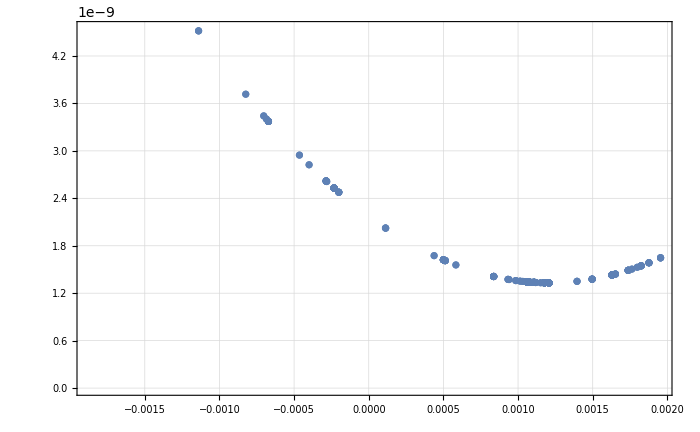

```mathematica
ListPlot[Table[{b,
Total[(PERCData180[[All,2]]-Table[FitFuncBinNormArith[bin,{b,Pi,0.2,0.2/1.5,0.2/1.5,4.,0.2/1.5+0.2/1.5*10^-4},{0.01,0.035,0.,0.,0.},XDatam70p05,3],{bin,1,32}])^2]},{b,drAFitPERC[[2,1]]}]]
```

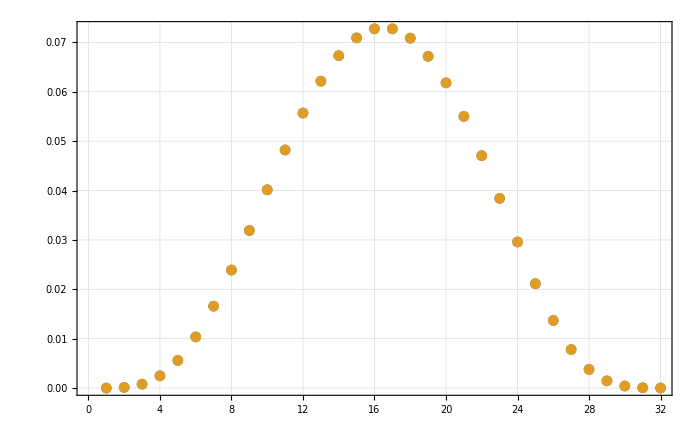

```mathematica
ListPlot[{PERCData180,Table[{bin,FitFuncBinNormArith[bin,{drAFitPERC[[1]]["BestFitParameters"][[1,2]],Pi,0.2,0.2/1.5,0.2/1.5,4.,0.2/1.5+0.2/1.5*10^-4},{0.01,0.035,0.,0.,0.},XDatam70p05,3]},{bin,1,32}]}]
```

# 90° but with filter!

### data

```mathematica
t0=AbsoluteTime[];
ILLData90WFilter=Table[{bin,FitFuncBinNormArith[bin,{0.,Pi/2,0.2,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDatam55p05,3]},{bin,1,Length[XDatam55p05]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.010828 and 0.00240031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26797 and 0.00317965 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.1044 and 0.00433095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.60251 and 0.00530303 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.9489 and 0.00586929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10023 and 0.00617257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.01576 and 0.00547174 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67541 and 0.00522039 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.750963 and 0.00289333 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271332 and 0.0148705 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423872 and 0.000119545 for the integral and error estimates.

403.520077

### took 470s

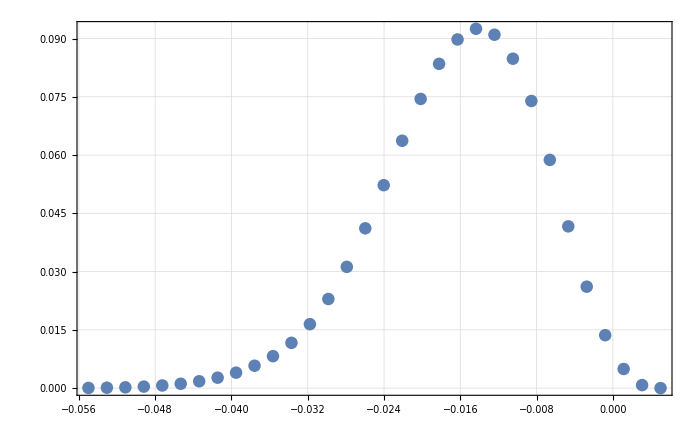

```mathematica
ListPlot[Transpose[{Reverse[XDatam55p05],ILLData90WFilter[[All,2]]}]]
```

```mathematica
Export["~/eclipse-workspace/TransportProject/TransportFunctions/GeneratedData/Electron_ILL90WFilter_Xm55p05_32Bins.txt",Transpose[{Reverse[XDatam55p05],ILLData90WFilter[[All,2]]}],"Table"];
```

fits

### dB fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
dBFit=Reap[NonlinearModelFit[
ILLData90WFilter,
{
FitFuncBinNormArith[bin,{b,Pi/2,0.2+0.2*5*10^-5,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDatam55p05,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->6,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Mon 9 Sep 2019 13:15:43

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108189 and 0.00239724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26774 and 0.00318934 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10442 and 0.0043809 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60258 and 0.00539105 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94904 and 0.00583332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10062 and 0.00617211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01614 and 0.00537371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67592 and 0.00520797 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.751093 and 0.00290106 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271388 and 0.0148712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423965 and 0.000119309 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108232 and 0.00239825 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26822 and 0.00319003 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10489 and 0.00432129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60293 and 0.00539155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94918 and 0.0058335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10052 and 0.00612525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01576 and 0.00538249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67533 and 0.00520711 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.750806 and 0.0029002 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271262 and 0.014867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423723 and 0.000119239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108235 and 0.00239833 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26826 and 0.00319008 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10492 and 0.00432134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60295 and 0.00539158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.9492 and 0.00583351 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10051 and 0.00612523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01573 and 0.00538245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67528 and 0.00520704 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.750784 and 0.00290014 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271252 and 0.0148666 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423705 and 0.000119233 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.010823 and 0.0023982 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.2682 and 0.00319 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10486 and 0.00432126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60291 and 0.00539152 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94918 and 0.00583349 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10053 and 0.00612526 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01578 and 0.00538252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67536 and 0.00520715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.75082 and 0.00290024 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271268 and 0.0148672 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423735 and 0.000119242 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108196 and 0.00239742 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26783 and 0.00318947 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.1045 and 0.00438101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60264 and 0.00539114 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94907 and 0.00583336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.1006 and 0.00617206 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01607 and 0.00537362 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67582 and 0.00520781 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.751041 and 0.00290091 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271366 and 0.0148704 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423921 and 0.000119296 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.010823 and 0.00239822 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26821 and 0.00319001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10487 and 0.00432127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60291 and 0.00539153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94918 and 0.0058335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10053 and 0.00612526 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01577 and 0.00538251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67535 and 0.00520714 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.750816 and 0.00290023 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271266 and 0.0148671 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423732 and 0.000119241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.010815 and 0.00239633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26731 and 0.00318873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10399 and 0.00438034 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60228 and 0.00539061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94892 and 0.00583316 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10072 and 0.00622741 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01646 and 0.00537416 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67645 and 0.00520873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.751347 and 0.00290183 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271501 and 0.014875 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0424179 and 0.000119371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108231 and 0.00239824 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26822 and 0.00319003 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10488 and 0.00432129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60292 and 0.00539154 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94918 and 0.0058335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10052 and 0.00612525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01576 and 0.0053825 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67533 and 0.00520712 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.750808 and 0.00290021 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271263 and 0.014867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423725 and 0.000119239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108166 and 0.00239671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26749 and 0.00318899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10417 and 0.00438057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.6024 and 0.00539079 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94897 and 0.00583323 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10068 and 0.00622731 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01633 and 0.00537397 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67623 and 0.00520842 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271454 and 0.0148734 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.751242 and 0.00290151 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.042409 and 0.000119345 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108147 and 0.00239626 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26728 and 0.00318868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10395 and 0.0043803 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60225 and 0.00539057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94891 and 0.00583315 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10073 and 0.00622744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01649 and 0.0053742 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67649 and 0.0052088 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.751369 and 0.00290189 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.27151 and 0.0148753 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0424197 and 0.000119376 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108232 and 0.00239825 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26822 and 0.00319003 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10489 and 0.00432129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60293 and 0.00539155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94918 and 0.0058335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10052 and 0.00612525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01576 and 0.00538249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67533 and 0.00520711 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.750806 and 0.0029002 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271262 and 0.014867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423723 and 0.000119239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108161 and 0.0023966 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26744 and 0.00318891 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10412 and 0.00438051 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60237 and 0.00539074 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94895 and 0.00583321 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10069 and 0.00622734 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01637 and 0.00537403 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67629 and 0.00520851 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.751273 and 0.0029016 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271468 and 0.0148739 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0424116 and 0.000119352 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108198 and 0.00239745 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26784 and 0.00318949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10452 and 0.00438103 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60265 and 0.00539115 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94907 and 0.00583336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.1006 and 0.00617205 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01606 and 0.0053736 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.6758 and 0.00520779 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.751033 and 0.00290088 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271362 and 0.0148703 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423914 and 0.000119294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108188 and 0.00239723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26774 and 0.00318934 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10441 and 0.00438089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60258 and 0.00539105 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94904 and 0.00583332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10062 and 0.00617211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01614 and 0.00537371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67593 and 0.00520798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.751095 and 0.00290107 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271389 and 0.0148712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423966 and 0.000119309 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108229 and 0.00239818 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26819 and 0.00318998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10485 and 0.00432125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.6029 and 0.00539151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94917 and 0.00583349 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10053 and 0.00612527 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01578 and 0.00538253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67537 and 0.00520717 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.750827 and 0.00290026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271271 and 0.0148673 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423741 and 0.000119244 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108236 and 0.00239835 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26827 and 0.0031901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10494 and 0.00432135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60296 and 0.00539159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.9492 and 0.00583352 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10051 and 0.00612522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01572 and 0.00538244 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67527 and 0.00520702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.750778 and 0.00290012 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271249 and 0.0148665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423699 and 0.000119232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108191 and 0.00239731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26777 and 0.00318939 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10445 and 0.00438094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60261 and 0.00539108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94905 and 0.00583333 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10062 and 0.00617209 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01611 and 0.00537368 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67588 and 0.00520791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.751073 and 0.002901 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.27138 and 0.0148709 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423948 and 0.000119304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108152 and 0.00239638 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26733 and 0.00318876 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10401 and 0.00438037 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60229 and 0.00539063 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94892 and 0.00583317 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10072 and 0.0062274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01645 and 0.00537414 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67642 and 0.0052087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.751335 and 0.00290179 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271495 and 0.0148748 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0424169 and 0.000119368 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108212 and 0.00239778 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.268 and 0.00318971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10464 and 0.00443237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60277 and 0.00539132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94912 and 0.00583342 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10057 and 0.00612538 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01594 and 0.00537344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.6756 and 0.00520751 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.750939 and 0.0029006 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271321 and 0.0148689 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423835 and 0.000119271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108145 and 0.00239621 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26726 and 0.00318865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10393 and 0.00438027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60224 and 0.00539055 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.9489 and 0.00583314 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10073 and 0.00622745 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01651 and 0.00537422 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67652 and 0.00520884 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.751381 and 0.00290193 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.271516 and 0.0148755 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0424208 and 0.000119379 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108219 and 0.00239795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26808 and 0.00318983 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10472 and 0.00443247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.60282 and 0.0053914 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 4.94914 and 0.00583345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.10056 and 0.00612533 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.01588 and 0.00537336 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.67551 and 0.00520737 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.750892 and 0.00290046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.2713 and 0.0148682 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0423795 and 0.00011926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.0108177 and 0.00239697 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.26761 and 0.00318916 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.10429 and 0.00438073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

9303.862958

### took 43751s or 12h

```mathematica
dBFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

```mathematica
dBFit[[1]]["BestFitParameters"]
```

{b→0.0001}

### rA fit

```mathematica
t0=AbsoluteTime[];
drAFit=Reap[NonlinearModelFit[
ILLData90WFilter,
{
FitFuncBinNormArith[bin,{b,Pi/2,0.2,1.,1.,2.,1.+1*10^-4},{0.01,0.035,0.,0.,0.},XDatam55p05,3],
-0.003<b<0.003
},
{{b,-0.0001}},bin,MaxIterations->10,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33494 and 0.00491556 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14663 and 0.00554188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0368 and 0.00899804 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4587 and 0.0150685 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4641 and 0.0271248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8607 and 0.0156766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0996 and 0.0141475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3595 and 0.0103893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94614 and 0.00516025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72824 and 0.0121518 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06072 and 0.0367203 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172704 and 0.0003855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33501 and 0.00491574 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14672 and 0.00554208 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03696 and 0.00899823 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4589 and 0.0150687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4641 and 0.0271247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8606 and 0.0156764 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0994 and 0.0141473 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3593 and 0.0103892 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94598 and 0.00516014 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06067 and 0.0367192 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72814 and 0.0121515 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172693 and 0.000385474 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33489 and 0.00491544 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14658 and 0.00554175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0367 and 0.00899792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4586 and 0.0150684 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.464 and 0.027125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8608 and 0.0156767 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0997 and 0.0141477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3597 and 0.0103893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94624 and 0.00516032 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06075 and 0.0367209 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7283 and 0.012152 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172711 and 0.000385516 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33419 and 0.00491358 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14568 and 0.00553973 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03511 and 0.00899599 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4569 and 0.015055 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1016 and 0.0141504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3622 and 0.0104251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94788 and 0.00516139 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72935 and 0.0121555 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06126 and 0.0367315 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17282 and 0.000385773 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3349 and 0.00491548 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14659 and 0.00554179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03673 and 0.00899795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4587 and 0.0150684 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.464 and 0.0271249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8608 and 0.0156767 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0997 and 0.0141476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3596 and 0.0103893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94621 and 0.0051603 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72829 and 0.012152 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06075 and 0.0367208 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172709 and 0.000385512 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3332 and 0.00488867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14444 and 0.00543444 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03293 and 0.00899873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4546 and 0.0150521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.026995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8637 and 0.0156778 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1043 and 0.0141541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3657 and 0.0104267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95016 and 0.00516288 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06196 and 0.0367462 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73081 and 0.0121602 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17297 and 0.00038613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33493 and 0.00491554 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14663 and 0.00554186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03678 and 0.00899802 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4587 and 0.0150685 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4641 and 0.0271249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8607 and 0.0156766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0996 and 0.0141475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3596 and 0.0103893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72825 and 0.0121519 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94616 and 0.00516026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06073 and 0.0367204 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172705 and 0.000385503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33355 and 0.00491188 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14487 and 0.00543538 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03369 and 0.00899965 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150531 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8631 and 0.015677 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1034 and 0.0141528 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3645 and 0.0104262 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94937 and 0.00516237 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73031 and 0.0121586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06172 and 0.0367411 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172918 and 0.000386007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33313 and 0.00488849 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14436 and 0.00543424 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03277 and 0.00899854 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4544 and 0.0150519 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0269952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8638 and 0.015678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1045 and 0.0141543 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.366 and 0.0104269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95032 and 0.00516299 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06201 and 0.0367472 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73091 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172981 and 0.000386155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33494 and 0.00491556 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14663 and 0.00554188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0368 and 0.00899804 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4587 and 0.0150685 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4641 and 0.0271248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8607 and 0.0156766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0996 and 0.0141475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3595 and 0.0103893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94614 and 0.00516025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72824 and 0.0121518 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06072 and 0.0367203 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172704 and 0.0003855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3335 and 0.00491175 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14481 and 0.00543524 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03358 and 0.00899952 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4553 and 0.0150529 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8632 and 0.0156771 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1035 and 0.014153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3647 and 0.0104262 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94949 and 0.00516244 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73038 and 0.0121588 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06175 and 0.0367418 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172926 and 0.000386025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33422 and 0.00491365 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14571 and 0.00553981 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03517 and 0.00899606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.457 and 0.0150551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1015 and 0.0141503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3621 and 0.010425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00516135 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72932 and 0.0121553 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06124 and 0.0367311 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172816 and 0.000385764 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33402 and 0.00491312 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14547 and 0.00544018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03474 and 0.00900093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4565 and 0.0150545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271272 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1021 and 0.014151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3628 and 0.0104254 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94828 and 0.00516166 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72961 and 0.0121563 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06138 and 0.0367341 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172846 and 0.000385836 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33487 and 0.00491539 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14655 and 0.00554169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03665 and 0.00899786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4586 and 0.0150683 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.464 and 0.027125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8608 and 0.0156768 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.0997 and 0.0141478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3598 and 0.0103894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94629 and 0.00516035 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72834 and 0.0121521 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06077 and 0.0367213 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172714 and 0.000385524 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33457 and 0.00491459 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14617 and 0.00554083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03598 and 0.00899704 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4579 and 0.0150675 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4639 and 0.0271258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8614 and 0.0157275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1006 and 0.0141489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3608 and 0.0104256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94699 and 0.00516081 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72878 and 0.0121536 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06098 and 0.0367258 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17276 and 0.000385633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33325 and 0.00488881 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14451 and 0.00543459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03305 and 0.00899887 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4547 and 0.0150522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0269949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8636 and 0.0156777 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1042 and 0.0141539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3655 and 0.0104266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95003 and 0.0051628 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73073 and 0.01216 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06192 and 0.0367454 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172962 and 0.00038611 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33309 and 0.00488839 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14431 and 0.00543414 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03268 and 0.00899843 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4543 and 0.0150518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0269953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8639 and 0.0156639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1046 and 0.0141545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3661 and 0.0104269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73097 and 0.0121607 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95041 and 0.00516305 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06204 and 0.0367478 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172987 and 0.000386169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33376 and 0.00491244 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14514 and 0.00543597 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03416 and 0.00900023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4559 and 0.0150537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0271278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8628 and 0.0157295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1028 and 0.014152 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3638 and 0.0104258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94888 and 0.00516205 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72999 and 0.0121576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06157 and 0.036738 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172886 and 0.00038593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33424 and 0.00491371 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14574 and 0.00553987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03522 and 0.00899612 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1015 and 0.0141502 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.362 and 0.010425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94777 and 0.00516132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121552 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06122 and 0.0367308 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172812 and 0.000385755 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33367 and 0.0049122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14502 and 0.00543572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03396 and 0.00899998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4557 and 0.0150534 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.027128 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8629 and 0.0157297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1031 and 0.0141523 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3641 and 0.010426 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94909 and 0.00516219 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73013 and 0.012158 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06163 and 0.0367393 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.1729 and 0.000385963 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33432 and 0.00491393 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14585 and 0.00554011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03541 and 0.00899635 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0150554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.0157281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1013 and 0.0141499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3617 and 0.0104249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94758 and 0.00516119 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72916 and 0.0121548 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06117 and 0.0367295 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172799 and 0.000385725 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33381 and 0.00491257 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14521 and 0.0054396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03427 and 0.00900036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.456 and 0.0150539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8627 and 0.0157293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1027 and 0.0141518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94877 and 0.00516197 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72992 and 0.0121573 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06153 and 0.0367372 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172878 and 0.000385912 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33309 and 0.00488838 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1443 and 0.00543413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03268 and 0.00899843 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4543 and 0.0150518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0269953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8639 and 0.0156639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1046 and 0.0141545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3661 and 0.0104269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95041 and 0.00516305 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73097 and 0.0121607 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06204 and 0.0367478 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172987 and 0.00038617 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33311 and 0.00488845 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14433 and 0.0054342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03273 and 0.00899849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4544 and 0.0150518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0269952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8639 and 0.0156639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1045 and 0.0141544 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.366 and 0.0104269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.95036 and 0.00516301 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73094 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06202 and 0.0367474 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172984 and 0.000386161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33445 and 0.00491426 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14601 and 0.00554047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03569 and 0.00899669 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4576 and 0.0150671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0271261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8616 and 0.0157278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1009 and 0.0141494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3613 and 0.0104246 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94728 and 0.005161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72897 and 0.0121542 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06107 and 0.0367276 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17278 and 0.000385679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33422 and 0.00491365 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14572 and 0.00553981 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03518 and 0.00899607 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.457 and 0.0150551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.862 and 0.0157283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1015 and 0.0141503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3621 and 0.010425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94782 and 0.00516135 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72931 and 0.0121553 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06124 and 0.0367311 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172815 and 0.000385763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33431 and 0.00491389 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14583 and 0.00554007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03537 and 0.00899631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4572 and 0.0150553 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.0157281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1013 and 0.0141499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3618 and 0.0104249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94761 and 0.00516122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72918 and 0.0121549 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06118 and 0.0367298 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172802 and 0.000385731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33374 and 0.00491238 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14511 and 0.00543591 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03411 and 0.00900017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4559 and 0.0150536 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4634 and 0.0271279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8628 and 0.0157295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1029 and 0.0141521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3638 and 0.0104258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94893 and 0.00516208 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73003 and 0.0121577 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06158 and 0.0367383 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172889 and 0.000385938 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33414 and 0.00491345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14562 and 0.0055396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.035 and 0.00899586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94799 and 0.00516146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72942 and 0.0121557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0367322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172827 and 0.00038579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33386 and 0.0049127 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14527 and 0.00543973 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03438 and 0.0090005 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.015054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8626 and 0.0157292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1025 and 0.0141516 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3634 and 0.0104256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94865 and 0.0051619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72985 and 0.0121571 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0615 and 0.0367365 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172871 and 0.000385894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33414 and 0.00491345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14562 and 0.0055396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.035 and 0.00899586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94799 and 0.00516146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72942 and 0.0121557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0367322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172827 and 0.00038579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3347 and 0.00491492 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14633 and 0.00554119 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03626 and 0.00899738 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4639 and 0.0271254 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8611 and 0.0156772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1002 and 0.0141484 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3604 and 0.0103897 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9467 and 0.00516062 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7286 and 0.012153 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06089 and 0.0367239 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172741 and 0.000385588 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33434 and 0.00491399 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14588 and 0.00554018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03546 and 0.00899641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4573 and 0.0150668 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0271263 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8618 and 0.015728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1012 and 0.0141498 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3617 and 0.0104248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94752 and 0.00516116 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72912 and 0.0121547 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06115 and 0.0367292 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172796 and 0.000385717 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33445 and 0.00491426 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14601 and 0.00554047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03569 and 0.00899669 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4576 and 0.0150671 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0271261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8616 and 0.0157278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1009 and 0.0141494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3613 and 0.0104246 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94728 and 0.005161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72897 and 0.0121542 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06108 and 0.0367277 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17278 and 0.000385679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33425 and 0.00491373 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14575 and 0.0055399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03524 and 0.00899615 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8619 and 0.0157283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1015 and 0.0141501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.362 and 0.010425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94775 and 0.0051613 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72927 and 0.0121552 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06122 and 0.0367306 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172811 and 0.000385752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33384 and 0.00491265 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14524 and 0.00543968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03434 and 0.00900044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0150539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8626 and 0.0157293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1026 and 0.0141517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3635 and 0.0104257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9487 and 0.00516193 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72988 and 0.0121572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06151 and 0.0367368 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172874 and 0.000385901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33416 and 0.0049135 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14564 and 0.00553965 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03505 and 0.00899591 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4569 and 0.0150549 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4637 and 0.0271268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3623 and 0.0104251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94795 and 0.00516144 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7294 and 0.0121556 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06128 and 0.0367319 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172824 and 0.000385783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33415 and 0.00491347 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14563 and 0.00553962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03502 and 0.00899588 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150549 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94797 and 0.00516145 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72941 and 0.0121557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0367321 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172826 and 0.000385788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33385 and 0.00491268 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14526 and 0.00543971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03436 and 0.00900047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.015054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8626 and 0.0157292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1026 and 0.0141517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3634 and 0.0104257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94867 and 0.00516191 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72986 and 0.0121571 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0615 and 0.0367366 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172872 and 0.000385897 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33414 and 0.00491345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14562 and 0.0055396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.035 and 0.00899586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94799 and 0.00516146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72942 and 0.0121557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0367322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172827 and 0.00038579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33395 and 0.00491294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14538 and 0.00543999 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03459 and 0.00900075 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4564 and 0.0150543 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271273 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8625 and 0.015729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1023 and 0.0141513 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3631 and 0.0104255 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94844 and 0.00516176 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72971 and 0.0121566 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06143 and 0.0367351 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172857 and 0.000385861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33384 and 0.00491265 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14524 and 0.00543967 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03434 and 0.00900044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0150539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8626 and 0.0157293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1026 and 0.0141517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3635 and 0.0104257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9487 and 0.00516193 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72988 and 0.0121572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06151 and 0.0367368 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172874 and 0.000385902 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33412 and 0.0049134 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1456 and 0.00544047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03496 and 0.0089958 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8622 and 0.0157286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1018 and 0.0141506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3625 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94804 and 0.0051615 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72946 and 0.0121558 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06131 and 0.0367325 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17283 and 0.000385798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33451 and 0.00491442 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14609 and 0.00554064 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03583 and 0.00899686 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4577 and 0.0150673 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4638 and 0.0271259 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8615 and 0.0157276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1007 and 0.0141492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3611 and 0.0104245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94714 and 0.00516091 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72888 and 0.0121539 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06103 and 0.0367267 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17277 and 0.000385657 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33409 and 0.00491331 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14556 and 0.00544038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03488 and 0.00899571 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4567 and 0.0150547 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.027127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8622 and 0.0157286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1019 and 0.0141507 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3626 and 0.0104253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94812 and 0.00516155 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7295 and 0.012156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06133 and 0.036733 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172835 and 0.00038581 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33405 and 0.00491321 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14551 and 0.00544027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03479 and 0.0089956 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0150546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.102 and 0.0141509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3627 and 0.0104253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94821 and 0.00516161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72956 and 0.0121561 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06136 and 0.0367336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172841 and 0.000385824 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33405 and 0.0049132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14551 and 0.00544026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03478 and 0.00899559 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0150546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.102 and 0.0141509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3627 and 0.0104253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94822 and 0.00516161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06136 and 0.0367337 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72957 and 0.0121562 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172842 and 0.000385826 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33414 and 0.00491345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.14562 and 0.0055396 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.035 and 0.00899586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271268 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8621 and 0.0157285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1017 and 0.0141505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104252 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94799 and 0.00516146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72942 and 0.0121557 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0367322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172827 and 0.00038579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3339 and 0.0049128 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14532 and 0.00543984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03447 and 0.0090006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4562 and 0.0150541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8625 and 0.0157291 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1024 and 0.0141515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3633 and 0.0104256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94857 and 0.00516184 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72979 and 0.0121569 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06147 and 0.0367359 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172865 and 0.000385881 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33388 and 0.00491276 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1453 and 0.0054398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03444 and 0.00900056 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4562 and 0.0150541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8626 and 0.0157292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1025 and 0.0141515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3633 and 0.0104256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9486 and 0.00516186 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72981 and 0.012157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06148 and 0.0367361 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172867 and 0.000385885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33406 and 0.00491324 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14553 and 0.00544031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03483 and 0.00899564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0150546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.027127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.102 and 0.0141508 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3627 and 0.0104253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94818 and 0.00516158 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72954 and 0.0121561 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06135 and 0.0367334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172839 and 0.000385819 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3339 and 0.00491282 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14533 and 0.00543986 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03448 and 0.00900062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4563 and 0.0150541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4635 and 0.0271274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8625 and 0.0157291 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.1024 and 0.0141515 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3632 and 0.0104256 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94855 and 0.00516183 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06147 and 0.0367358 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72978 and 0.0121569 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172864 and 0.000385878 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33405 and 0.00491321 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14551 and 0.00544027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03479 and 0.0089956 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4566 and 0.0150546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4636 and 0.0271271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 14.8623 and 0.0157287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.102 and 0.0141509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.3627 and 0.0104253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94821 and 0.00516161 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72956 and 0.0121561 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06136 and 0.0367336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172841 and 0.000385824 for the integral and error estimates.

22516.43869

### took 22516 s or 6,25h

```mathematica
drAFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0000750132 | 0.0000470927 | 1.59288 | 0.121333

### Alpha Fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
dAlphaFit=Reap[NonlinearModelFit[
ILLData90WFilter,
{
FitFuncBinNormArith[bin,{b,Pi/2+Pi/2*5*10^-5,0.2,1.,1.,2.,1.},{0.01,0.035,0.,0.,0.},XDatam55p05,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->5,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Fri 28 Jun 2019 00:27:23

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33444 and 0.00487253 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14592 and 0.00545471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03537 and 0.0089724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.0150381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0271087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8612 and 0.0154286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3614 and 0.0104483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94748 and 0.00531564 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72909 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0609 and 0.0367961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172799 and 0.000376151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33505 and 0.00487413 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1467 and 0.00545642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03675 and 0.00897407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94604 and 0.00514749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72818 and 0.0121576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06047 and 0.0367869 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172705 and 0.000375935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33509 and 0.00487425 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14676 and 0.00545655 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03685 and 0.0089742 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4584 and 0.015018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271071 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8601 and 0.0154271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3591 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94593 and 0.00514742 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72811 and 0.0121574 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06043 and 0.0367862 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172697 and 0.000375918 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33502 and 0.00487406 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14666 and 0.00545633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03668 and 0.00897399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3594 and 0.010413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94611 and 0.00514754 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72822 and 0.0121578 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06049 and 0.0367874 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172709 and 0.000375945 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33455 and 0.00487282 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14606 and 0.00545501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03562 and 0.0089727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8611 and 0.0154283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3611 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94719 and 0.00514047 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72892 and 0.01216 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06082 and 0.0367944 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172782 and 0.000376112 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33502 and 0.00487408 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14667 and 0.00545636 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0367 and 0.00897401 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.010413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94609 and 0.00514753 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72821 and 0.0121577 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06048 and 0.0367872 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172708 and 0.000375942 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.3339 and 0.00487111 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14523 and 0.00545319 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03419 and 0.00896316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4555 and 0.0150364 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8622 and 0.0154298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3634 and 0.0104492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94874 and 0.00531653 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72989 and 0.0121632 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06129 and 0.0368042 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172882 and 0.000376344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33504 and 0.00487412 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14669 and 0.0054564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03674 and 0.00897405 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94605 and 0.0051475 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72819 and 0.0121576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06047 and 0.036787 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172705 and 0.000375937 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33412 and 0.0048717 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14552 and 0.00545382 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03466 and 0.00897153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.456 and 0.0150371 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4628 and 0.0271095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8618 and 0.0154293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3626 and 0.0104488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94821 and 0.00531616 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72956 and 0.0121621 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06113 and 0.0368008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172847 and 0.000376264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33385 and 0.00487099 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14517 and 0.00545306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03409 and 0.00896304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8623 and 0.0154299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72996 and 0.0121634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94884 and 0.00531661 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06133 and 0.0368049 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172889 and 0.00037636 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33505 and 0.00487413 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1467 and 0.00545642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03675 and 0.00897407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4582 and 0.0150179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271072 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8602 and 0.0154272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3593 and 0.0104129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94604 and 0.00514749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72818 and 0.0121576 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06047 and 0.0367869 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172705 and 0.000375935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33406 and 0.00487153 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14543 and 0.00545363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03451 and 0.00897135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4559 and 0.0150369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4628 and 0.0271097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8619 and 0.0154294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3628 and 0.0104489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94837 and 0.00531627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72966 and 0.0121624 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06118 and 0.0368018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172858 and 0.000376287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33457 and 0.00487287 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14609 and 0.00545506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03566 and 0.00897275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271084 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.861 and 0.0154283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.361 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94715 and 0.00514044 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7289 and 0.01216 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06081 and 0.0367942 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172779 and 0.000376106 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33443 and 0.00487252 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14592 and 0.00545469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03536 and 0.00897239 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.015038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0271087 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8613 and 0.0154286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3615 and 0.0104483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94749 and 0.00531565 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72909 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06091 and 0.0367961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172799 and 0.000376153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.335 and 0.00487402 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14664 and 0.00545629 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03665 and 0.00897395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4581 and 0.0150178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4633 and 0.0271073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8603 and 0.0154273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3594 and 0.010413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94614 and 0.00514756 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72824 and 0.0121578 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0605 and 0.0367876 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172711 and 0.00037595 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33482 and 0.00487353 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14641 and 0.00545577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03623 and 0.00897344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4577 and 0.0150172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.0271078 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8606 and 0.0154277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3601 and 0.010425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94658 and 0.00514784 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06063 and 0.0367904 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72852 and 0.0121587 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17274 and 0.000376017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33393 and 0.0048712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14528 and 0.00545329 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03427 and 0.00896326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4556 and 0.0150366 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.02711 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8621 and 0.0154297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3633 and 0.0104491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94865 and 0.00531647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72984 and 0.012163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06127 and 0.0368037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172877 and 0.000376331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33383 and 0.00487092 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14514 and 0.00545299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03403 and 0.00896297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4553 and 0.0150362 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271103 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8623 and 0.0154299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9489 and 0.00531665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06134 and 0.0368053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.73 and 0.0121636 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172893 and 0.000376369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33424 and 0.00487202 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14567 and 0.00545416 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03493 and 0.00897186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4563 and 0.0150375 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8616 and 0.015429 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3622 and 0.0104486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94793 and 0.00531596 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72938 and 0.0121615 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06104 and 0.036799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172829 and 0.000376221 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33461 and 0.004873 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14615 and 0.0054552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03577 and 0.00897288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4572 and 0.0150386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8609 and 0.0154282 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3608 and 0.010448 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94704 and 0.00514037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72882 and 0.0121597 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06078 and 0.0367934 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172771 and 0.000376089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33474 and 0.00487334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14631 and 0.00545556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03606 and 0.00897324 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4575 and 0.015017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.027108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8607 and 0.0154279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3603 and 0.0104478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94675 and 0.00514795 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72863 and 0.0121591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06068 and 0.0367915 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172751 and 0.000376043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33385 and 0.00487097 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14516 and 0.00545304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03407 and 0.00896302 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271102 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8623 and 0.0154299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3636 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94886 and 0.00531662 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72997 and 0.0121635 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06133 and 0.036805 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17289 and 0.000376363 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33401 and 0.00487139 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14537 and 0.00545349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03444 and 0.00896346 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4557 and 0.0150368 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4628 and 0.0271098 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.862 and 0.0154295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.363 and 0.010449 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94849 and 0.00531635 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72973 and 0.0121627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06121 and 0.0368026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172866 and 0.000376306 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33431 and 0.00487219 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14575 and 0.00545434 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03508 and 0.00897204 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4565 and 0.0150377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8615 and 0.0154289 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3619 and 0.0104485 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94778 and 0.00531586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.061 and 0.036798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72928 and 0.0121612 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172819 and 0.000376198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33443 and 0.00487251 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14591 and 0.00545468 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03535 and 0.00897237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4568 and 0.015038 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.463 and 0.0271088 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8613 and 0.0154286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3615 and 0.0104483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9475 and 0.00531566 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.7291 and 0.0121606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06091 and 0.0367962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.1728 and 0.000376155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33458 and 0.0048729 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1461 and 0.0054551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03569 and 0.00897278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4571 and 0.0150385 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.861 and 0.0154283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3609 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94713 and 0.00514043 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0608 and 0.036794 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72888 and 0.0121599 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172777 and 0.000376102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33387 and 0.00487104 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.1452 and 0.00545311 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03413 and 0.00896309 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4554 and 0.0150364 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.0271101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8622 and 0.0154298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3635 and 0.0104493 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.9488 and 0.00531658 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72994 and 0.0121634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06131 and 0.0368046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172887 and 0.000376354 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33394 and 0.00487121 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14528 and 0.00545329 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03428 and 0.00896326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4556 and 0.0150366 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4627 and 0.02711 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8621 and 0.0154297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3633 and 0.0104491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94865 and 0.00531647 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72984 and 0.012163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06127 and 0.0368036 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172877 and 0.000376331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33454 and 0.00487279 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14605 and 0.00545499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0356 and 0.00897267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.457 and 0.0150384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4631 and 0.0271085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8611 and 0.0154284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3611 and 0.0104481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94722 and 0.00514049 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72894 and 0.0121601 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06083 and 0.0367946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172783 and 0.000376116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33417 and 0.00487182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14558 and 0.00545395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03476 and 0.00897166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0150373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8617 and 0.0154292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94811 and 0.00531609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0611 and 0.0368001 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72949 and 0.0121619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17284 and 0.000376247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33474 and 0.00487332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14631 and 0.00545555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03605 and 0.00897322 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4575 and 0.015017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4632 and 0.027108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8607 and 0.0154279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3604 and 0.0104478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94676 and 0.00514796 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72864 and 0.0121591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06069 and 0.0367916 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172752 and 0.000376045 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33432 and 0.00487222 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14577 and 0.00545437 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.0351 and 0.00897207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4565 and 0.0150377 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.027109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8615 and 0.0154288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3619 and 0.0104485 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94776 and 0.00531584 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72927 and 0.0121612 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.06099 and 0.0367979 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.172817 and 0.000376194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 2.33417 and 0.00487182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.14558 and 0.00545395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.03476 and 0.00897166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 10.4561 and 0.0150373 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.4629 and 0.0271094 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 14.8617 and 0.0154292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 10.3624 and 0.0104488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 4.94811 and 0.00531609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.72949 and 0.0121619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.0611 and 0.0368001 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.17284 and 0.000376247 for the integral and error estimates.

13770.33362

### took 13770s or 3,8h

```mathematica
dAlphaFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.000916626 | 0.0000928275 | 9.87451 | 4.32917×10^-11

```mathematica
dAlphaFit[[1]]["BestFitParameters"][[1,2]]/(5*10^-5)
```

18.3325

# 180° no filter

Data 180° no Filter

```mathematica
XDatam85p05=XDataCreation[{-0.085,0.005,0.},32]
```

{-0.085,-0.0820968,-0.0791935,-0.0762903,-0.0733871,-0.0704839,-0.0675806,-0.0646774,-0.0617742,-0.058871,-0.0559677,-0.0530645,-0.0501613,-0.0472581,-0.0443548,-0.0414516,-0.0385484,-0.0356452,-0.0327419,-0.0298387,-0.0269355,-0.0240323,-0.021129,-0.0182258,-0.0153226,-0.0124194,-0.00951613,-0.0066129,-0.00370968,-0.000806452,0.00209677,0.005}

```mathematica
t0=AbsoluteTime[];
ILLData180noFilter=Table[{bin,FitFuncBinNormArith[bin,{0.,Pi,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam85p05,3]},{bin,1,Length[XDatam85p05]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15781 and 0.00348409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14876 and 0.00971364 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50206 and 0.00832328 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03134 and 0.00891677 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43525 and 0.00404331 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198118 and 0.000214276 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289792 and 0.0000757957 for the integral and error estimates.

438.364107

### 438s

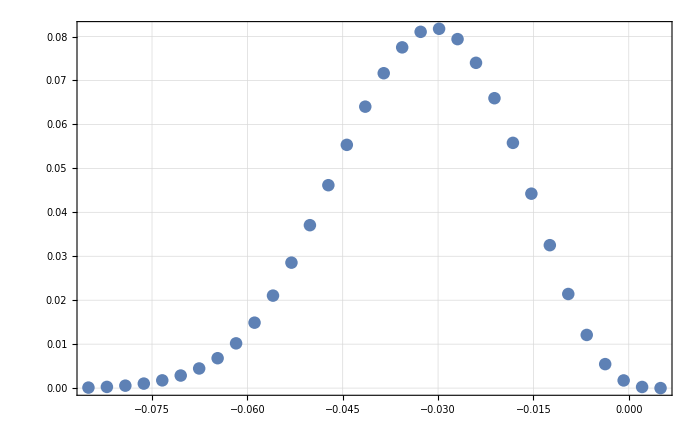

```mathematica
ListPlot[Transpose[{Reverse[XDatam85p05],ILLData180noFilter[[All,2]]}]]
```

```mathematica
(*Export["~/Dropbox/PhD/ElectronTransportSpectrum.txt",Transpose[{Reverse[XDatam55p05],ILLData90noFilter[[All,2]]}],"Table"]*)
```

~/Dropbox/PhD/ElectronTransportSpectrum.txt

Fits

### drRxB fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
drRxBFit=Reap[NonlinearModelFit[
ILLData180noFilter,
{
FitFuncBinNormArith[bin,{b,Pi,0.2,1./2+1/2.*10^-4,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam85p05,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->6,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Tue 29 Oct 2019 18:10:23

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15783 and 0.00349489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14792 and 0.00972054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50154 and 0.00832579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03112 and 0.0089048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43517 and 0.00407229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198117 and 0.000219737 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289837 and 0.0000773716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15821 and 0.00349626 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14899 and 0.00972169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.5001 and 0.00832466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.02944 and 0.00890401 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43404 and 0.00407084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.197998 and 0.000219606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289656 and 0.0000773233 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15824 and 0.00349636 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14907 and 0.00972178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.49999 and 0.00832458 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.02931 and 0.00890395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43395 and 0.00407073 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.197989 and 0.000219596 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289642 and 0.0000773197 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15819 and 0.00349619 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14894 and 0.00972163 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50017 and 0.00832472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.02952 and 0.00890405 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43409 and 0.00407091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198003 and 0.000219613 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289665 and 0.0000773257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1579 and 0.00349514 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14811 and 0.00972075 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50128 and 0.00832559 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03081 and 0.00890466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43497 and 0.00407203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198096 and 0.000219714 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289805 and 0.0000773629 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1582 and 0.00349621 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14895 and 0.00972165 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50015 and 0.0083247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.0295 and 0.00890404 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43408 and 0.00407089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198002 and 0.000219611 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289662 and 0.000077325 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1575 and 0.00349367 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14697 and 0.00971952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50282 and 0.00832679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03261 and 0.00890551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43618 and 0.00407358 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198223 and 0.000219854 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289999 and 0.0000774145 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15821 and 0.00349625 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14898 and 0.00972168 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50011 and 0.00832467 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.02945 and 0.00890402 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43405 and 0.00407086 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.197999 and 0.000219607 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289657 and 0.0000773237 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15764 and 0.00349418 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14737 and 0.00971994 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50229 and 0.00832637 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03199 and 0.00890522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43577 and 0.00407305 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198179 and 0.000219805 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289932 and 0.0000773967 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15747 and 0.00349357 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14689 and 0.00971943 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50293 and 0.00832687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03274 and 0.00890557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43627 and 0.00407369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198232 and 0.000219863 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0290012 and 0.0000774182 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15821 and 0.00349626 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14899 and 0.00972169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.5001 and 0.00832466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.02944 and 0.00890401 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43404 and 0.00407084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.197998 and 0.000219606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289656 and 0.0000773233 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1576 and 0.00349403 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14725 and 0.00971982 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50245 and 0.0083265 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03217 and 0.0089053 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43589 and 0.0040732 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198192 and 0.000219819 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289951 and 0.0000774019 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15791 and 0.00349518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14815 and 0.00972078 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50124 and 0.00832555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03077 and 0.00890464 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43494 and 0.00407199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198092 and 0.00021971 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289799 and 0.0000773615 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15783 and 0.00349488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14791 and 0.00972053 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50155 and 0.0083258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03113 and 0.00890481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43518 and 0.0040723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198118 and 0.000219738 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289839 and 0.000077372 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15818 and 0.00349616 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14891 and 0.00972161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.5002 and 0.00832475 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.02956 and 0.00890407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43412 and 0.00407095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198006 and 0.000219616 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289669 and 0.0000773268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15807 and 0.00349574 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14859 and 0.00972125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50064 and 0.00832509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03007 and 0.00890431 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43447 and 0.00407139 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198043 and 0.000219656 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289725 and 0.0000773416 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15752 and 0.00349375 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14703 and 0.00971959 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50274 and 0.00832672 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03251 and 0.00890546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43612 and 0.0040735 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198216 and 0.000219846 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289988 and 0.0000774117 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15745 and 0.00349351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14685 and 0.00971938 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50299 and 0.00832692 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03281 and 0.0089056 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43632 and 0.00407375 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198237 and 0.000219869 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.029002 and 0.0000774202 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15771 and 0.00349445 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14758 and 0.00972017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50201 and 0.00832615 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03166 and 0.00890506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43554 and 0.00407276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198156 and 0.000219779 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289896 and 0.0000773871 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15794 and 0.00349529 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14823 and 0.00972087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50112 and 0.00832546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03063 and 0.00890457 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43485 and 0.00407187 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198083 and 0.000219699 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289785 and 0.0000773577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15769 and 0.00349436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14751 and 0.00972009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.5021 and 0.00832623 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03177 and 0.00890511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43562 and 0.00407286 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198164 and 0.000219788 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289908 and 0.0000773904 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15792 and 0.00349519 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14816 and 0.00972079 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50122 and 0.00832554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03075 and 0.00890463 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43492 and 0.00407197 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198091 and 0.000219708 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289797 and 0.0000773609 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15776 and 0.00349462 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14771 and 0.00972031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50183 and 0.00832601 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03145 and 0.00890496 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.4354 and 0.00407258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198141 and 0.000219763 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289874 and 0.0000773813 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15745 and 0.00349351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14684 and 0.00971938 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.503 and 0.00832692 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03281 and 0.00890561 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43632 and 0.00407376 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198238 and 0.000219869 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.029002 and 0.0000774203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15746 and 0.00349354 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14687 and 0.00971941 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50296 and 0.00832689 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03277 and 0.00890558 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43629 and 0.00407372 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198234 and 0.000219866 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0290016 and 0.0000774191 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15801 and 0.00349554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14843 and 0.00972109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50086 and 0.00832526 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03032 and 0.00890443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43464 and 0.00407161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.19806 and 0.000219675 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289751 and 0.0000773487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15787 and 0.00349504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14804 and 0.00972067 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50138 and 0.00832567 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03094 and 0.00890472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43505 and 0.00407214 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198104 and 0.000219723 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289818 and 0.0000773664 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15797 and 0.00349537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.1483 and 0.00972095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50103 and 0.00832539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03053 and 0.00890452 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43477 and 0.00407178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198075 and 0.000219691 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289773 and 0.0000773546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15771 and 0.00349446 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14759 and 0.00972018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50199 and 0.00832614 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03164 and 0.00890505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43553 and 0.00407275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198155 and 0.000219778 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289894 and 0.0000773867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15787 and 0.00349503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14803 and 0.00972066 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.5014 and 0.00832568 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03095 and 0.00890472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43506 and 0.00407215 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198105 and 0.000219724 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289819 and 0.0000773667 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1578 and 0.00349476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14782 and 0.00972043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50167 and 0.00832589 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03127 and 0.00890488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43528 and 0.00407243 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198128 and 0.000219749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289854 and 0.0000773761 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15787 and 0.00349504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14804 and 0.00972066 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50138 and 0.00832567 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03094 and 0.00890472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43505 and 0.00407214 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198104 and 0.000219723 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289818 and 0.0000773664 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.1581 and 0.00349586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14868 and 0.00972135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50052 and 0.00832499 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.02993 and 0.00890424 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43437 and 0.00407127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198032 and 0.000219645 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289709 and 0.0000773374 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15797 and 0.0034954 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14832 and 0.00972097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50101 and 0.00832537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03049 and 0.00890451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43475 and 0.00407175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198073 and 0.000219689 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.028977 and 0.0000773537 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15796 and 0.00349535 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14828 and 0.00972093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50105 and 0.00832541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03055 and 0.00890454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43479 and 0.0040718 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198077 and 0.000219693 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289776 and 0.0000773553 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15783 and 0.00349489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14792 and 0.00972054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50154 and 0.00832579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03112 and 0.0089048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43517 and 0.00407229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198117 and 0.000219737 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289837 and 0.0000773716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15783 and 0.00349489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14792 and 0.00972054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50154 and 0.00832579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03112 and 0.0089048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43517 and 0.00407229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198117 and 0.000219737 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289837 and 0.0000773716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15783 and 0.00349489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14792 and 0.00972054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50154 and 0.00832579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03112 and 0.0089048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43517 and 0.00407229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198117 and 0.000219737 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289837 and 0.0000773716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.787918 and 0.00211175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.10337 and 0.00892662 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.91326 and 0.00910881 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.68233 and 0.0113718 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.54539 and 0.00493726 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.314912 and 0.000369259 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0467244 and 0.000123614 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.787918 and 0.00211175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.10337 and 0.00892662 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.91326 and 0.00910881 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.68233 and 0.0113718 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 3.54539 and 0.00493726 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.314912 and 0.000369259 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0467244 and 0.000123614 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15783 and 0.00349489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14792 and 0.00972054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50154 and 0.00832579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03112 and 0.0089048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43517 and 0.00407229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198117 and 0.000219737 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289837 and 0.0000773716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15783 and 0.00349489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14792 and 0.00972054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50154 and 0.00832579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03112 and 0.0089048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43517 and 0.00407229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198117 and 0.000219737 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289837 and 0.0000773716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.706534 and 0.00182485 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.87324 and 0.00866084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.87323 and 0.00804014 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.22427 and 0.00948662 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.04282 and 0.011534 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.7909 and 0.00566168 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.340618 and 0.000380572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0506185 and 0.000133766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.706534 and 0.00182485 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 6.87324 and 0.00866084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.87323 and 0.00804014 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 9.22427 and 0.00948662 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 7.04282 and 0.011534 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 3.7909 and 0.00566168 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.340618 and 0.000380572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0506185 and 0.000133766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15783 and 0.00349489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14792 and 0.00972054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50154 and 0.00832579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03112 and 0.0089048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43517 and 0.00407229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198117 and 0.000219737 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289837 and 0.0000773716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15783 and 0.00349489 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14792 and 0.00972054 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50154 and 0.00832579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03112 and 0.0089048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43517 and 0.00407229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198117 and 0.000219737 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289837 and 0.0000773716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15785 and 0.00349494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14796 and 0.00972058 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50149 and 0.00832575 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03105 and 0.00890477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43513 and 0.00407224 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198113 and 0.000219732 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289831 and 0.0000773698 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15785 and 0.00349494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14796 and 0.00972058 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50149 and 0.00832575 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03105 and 0.00890477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43513 and 0.00407224 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198113 and 0.000219732 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289831 and 0.0000773698 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15785 and 0.00349494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14796 and 0.00972058 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50149 and 0.00832575 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03105 and 0.00890477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43513 and 0.00407224 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198113 and 0.000219732 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289831 and 0.0000773698 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 1.15785 and 0.00349494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 8.14796 and 0.00972058 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50149 and 0.00832575 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03105 and 0.00890477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43513 and 0.00407224 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198113 and 0.000219732 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289831 and 0.0000773698 for the integral and error estimates.

21074.01455

### took 21074s or 5.9h

```mathematica
drRxBFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | 0.0000307441 | 0.0000551433 | 0.557531 | 0.581169

```mathematica
drRxBFit[[1]]["BestFitParameters"][[1,2]]/(10^-4)
```

0.307441

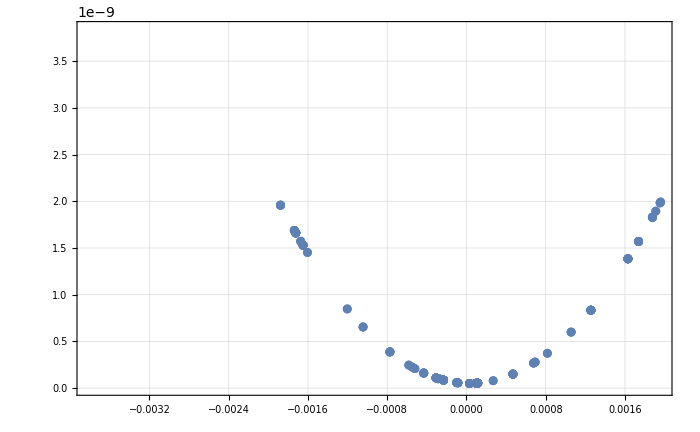

```mathematica
Chi2Plot[ILLData180noFilter[[All,2]],FitFuncBinNormArith[bini,{b,Pi,0.2,1./2+1/2.*10^-4,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam85p05,3],drRxBFit[[2,1]]]
```

### dB fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
dBFit=Reap[NonlinearModelFit[
ILLData180noFilter,
{
FitFuncBinNormArith[bin,{b,Pi,0.2+0.2*5*10^-5,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam85p05,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->6,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Wed 30 Oct 2019 17:10:43

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.1574 and 0.00348815 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14889 and 0.00972048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50317 and 0.00845665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03219 and 0.00892802 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.4357 and 0.00405606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198146 and 0.00021041 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289764 and 0.0000782613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15778 and 0.00348951 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14996 and 0.00972163 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50172 and 0.00845551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03051 and 0.00892721 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43456 and 0.00405461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198026 and 0.000210288 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289583 and 0.0000782125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15781 and 0.00348962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.15004 and 0.00972172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50161 and 0.00845543 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03038 and 0.00892715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43447 and 0.0040545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198017 and 0.000210278 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289569 and 0.0000782088 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15776 and 0.00348945 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.1499 and 0.00972158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50179 and 0.00845557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03059 and 0.00892725 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43462 and 0.00405468 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198032 and 0.000210293 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289592 and 0.0000782148 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15747 and 0.00348839 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14908 and 0.00972069 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50291 and 0.00845645 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03189 and 0.00892787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43549 and 0.00405579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198124 and 0.000210388 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289732 and 0.0000782525 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15776 and 0.00348947 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14992 and 0.00972159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50177 and 0.00845555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03057 and 0.00892724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.4346 and 0.00405466 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.19803 and 0.000210292 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289589 and 0.0000782142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15706 and 0.00348693 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14794 and 0.00971946 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50445 and 0.00845767 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03368 and 0.00892874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43671 and 0.00405734 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198252 and 0.000210519 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289926 and 0.0000783047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15777 and 0.0034895 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14995 and 0.00972162 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50173 and 0.00845552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03053 and 0.00892722 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43457 and 0.00405463 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198027 and 0.000210288 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289585 and 0.0000782129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.1572 and 0.00348743 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14833 and 0.00971988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50392 and 0.00845725 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03306 and 0.00892844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43629 and 0.0040568 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198208 and 0.000210474 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289859 and 0.0000782866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15703 and 0.00348683 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14785 and 0.00971937 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50456 and 0.00845776 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03381 and 0.0089288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43679 and 0.00405745 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198261 and 0.000210529 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289939 and 0.0000783084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15778 and 0.00348951 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14996 and 0.00972163 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50172 and 0.00845551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03051 and 0.00892721 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43456 and 0.00405461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198026 and 0.000210288 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289583 and 0.0000782125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15716 and 0.00348729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14821 and 0.00971976 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50407 and 0.00845737 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03324 and 0.00892853 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43641 and 0.00405696 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198221 and 0.000210487 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289878 and 0.0000782919 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15748 and 0.00348843 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14911 and 0.00972072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50286 and 0.00845642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03184 and 0.00892785 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43546 and 0.00405575 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198121 and 0.000210385 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289726 and 0.0000782511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.1574 and 0.00348814 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14888 and 0.00972047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50318 and 0.00845666 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.0322 and 0.00892803 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43571 and 0.00405607 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198147 and 0.000210411 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289766 and 0.0000782617 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15775 and 0.00348942 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14988 and 0.00972155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50183 and 0.0084556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03063 and 0.00892727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43464 and 0.00405472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198035 and 0.000210296 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289596 and 0.000078216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15781 and 0.00348965 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.15006 and 0.00972174 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50158 and 0.0084554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03035 and 0.00892713 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43445 and 0.00405447 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198014 and 0.000210275 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289565 and 0.0000782077 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15742 and 0.00348824 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14896 and 0.00972056 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50307 and 0.00845658 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03208 and 0.00892797 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43562 and 0.00405596 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198138 and 0.000210402 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289752 and 0.000078258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15708 and 0.00348699 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14798 and 0.00971951 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50439 and 0.00845762 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03361 and 0.0089287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43666 and 0.00405727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198247 and 0.000210514 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289918 and 0.0000783025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.1576 and 0.00348888 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14946 and 0.0097211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50239 and 0.00845604 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03129 and 0.00892759 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43509 and 0.00405528 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198082 and 0.000210344 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289667 and 0.0000782351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15702 and 0.00348677 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14781 and 0.00971932 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50462 and 0.0084578 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03459 and 0.0096691 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43684 and 0.00405751 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198266 and 0.000210534 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289947 and 0.0000783104 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15766 and 0.0034891 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14964 and 0.00972129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50215 and 0.00845586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03101 and 0.00892746 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.4349 and 0.00405505 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198062 and 0.000210324 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289637 and 0.0000782271 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.1573 and 0.00348778 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.1486 and 0.00972017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50355 and 0.00845696 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03264 and 0.00892824 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.436 and 0.00405644 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198178 and 0.000210443 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289813 and 0.0000782743 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15725 and 0.00348761 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14847 and 0.00972003 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50373 and 0.0084571 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03284 and 0.00892833 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43614 and 0.00405662 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198192 and 0.000210458 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289835 and 0.0000782803 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15775 and 0.00348941 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14987 and 0.00972154 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50183 and 0.0084556 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03064 and 0.00892728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43465 and 0.00405472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198035 and 0.000210297 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289597 and 0.0000782162 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15734 and 0.00348795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14873 and 0.00972031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50337 and 0.00845682 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03243 and 0.00892814 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43586 and 0.00405626 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198163 and 0.000210428 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.028979 and 0.0000782683 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15765 and 0.00348907 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14961 and 0.00972126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50219 and 0.00845588 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03106 and 0.00892748 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43493 and 0.00405508 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198065 and 0.000210327 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289642 and 0.0000782283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15779 and 0.00348957 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.15 and 0.00972168 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50166 and 0.00845547 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03044 and 0.00892718 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43451 and 0.00405455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198021 and 0.000210282 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289576 and 0.0000782105 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.1578 and 0.00348959 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.15001 and 0.00972169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50165 and 0.00845545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03042 and 0.00892717 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.4345 and 0.00405454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.19802 and 0.000210281 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289574 and 0.00007821 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15765 and 0.00348904 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14959 and 0.00972123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50222 and 0.00845591 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03109 and 0.00892749 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43495 and 0.00405511 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198068 and 0.00021033 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289646 and 0.0000782293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15777 and 0.00348948 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14993 and 0.0097216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50176 and 0.00845554 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03055 and 0.00892723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43459 and 0.00405465 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198029 and 0.00021029 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289587 and 0.0000782137 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15756 and 0.00348873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14934 and 0.00972097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50255 and 0.00845617 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03148 and 0.00892768 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43522 and 0.00405544 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198095 and 0.000210358 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289688 and 0.0000782406 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15775 and 0.00348943 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14989 and 0.00972156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50181 and 0.00845558 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03062 and 0.00892726 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43463 and 0.0040547 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198034 and 0.000210295 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289594 and 0.0000782155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15769 and 0.00348918 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14969 and 0.00972135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50207 and 0.00845579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03092 and 0.00892741 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43484 and 0.00405497 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198055 and 0.000210317 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289627 and 0.0000782244 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15755 and 0.00348869 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14931 and 0.00972094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50259 and 0.0084562 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03152 and 0.0089277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43524 and 0.00405548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198098 and 0.000210361 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289692 and 0.0000782418 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15749 and 0.00348849 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14916 and 0.00972077 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.5028 and 0.00845637 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03177 and 0.00892782 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43541 and 0.00405569 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198116 and 0.000210379 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289719 and 0.000078249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15724 and 0.00348755 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14842 and 0.00971998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50379 and 0.00845715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03291 and 0.00892837 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43619 and 0.00405668 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198197 and 0.000210463 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289843 and 0.0000782823 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15752 and 0.00348857 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14922 and 0.00972084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50272 and 0.0084563 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03167 and 0.00892777 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43535 and 0.00405561 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198109 and 0.000210372 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289708 and 0.0000782462 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15738 and 0.00348809 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14884 and 0.00972043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50322 and 0.0084567 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03226 and 0.00892805 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43574 and 0.00405611 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198151 and 0.000210415 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289772 and 0.0000782633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15744 and 0.0034883 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14901 and 0.00972061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.503 and 0.00845653 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.032 and 0.00892793 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43557 and 0.00405589 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198132 and 0.000210397 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289744 and 0.0000782558 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.1576 and 0.00348888 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14946 and 0.0097211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50239 and 0.00845604 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03129 and 0.00892759 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43509 and 0.00405528 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198082 and 0.000210344 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289667 and 0.0000782351 for the integral and error estimates.

16906.93042

### took 16906s or 4.7h

```mathematica
dBFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | -0.00088704 | 0.000129976 | -6.82464 | 1.20369×10^-7

```mathematica
dBFit[[1]]["BestFitParameters"][[1,2]]/(5*10^-5)
```

-17.7408

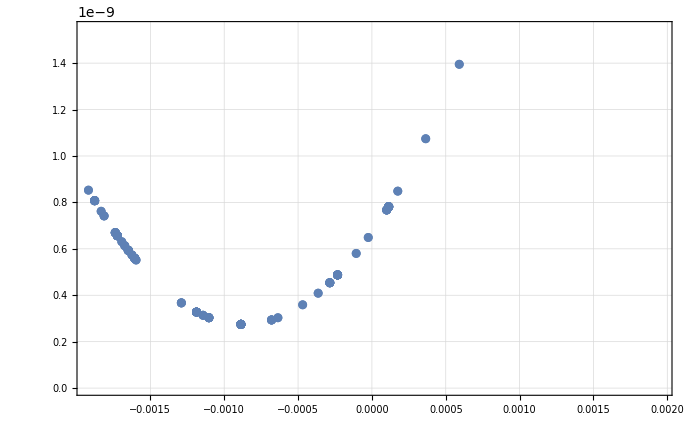

```mathematica
Chi2Plot[ILLData180noFilter[[All,2]],FitFuncBinNormArith[bini,{b,Pi,0.2+0.2*5*10^-5,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},XDatam85p05,3],dBFit[[2,1]]]
```

### rA fit

```mathematica
t0=AbsoluteTime[];
drAFit=Reap[NonlinearModelFit[
ILLData180noFilter,
{
FitFuncBinNormArith[bin,{b,Pi,0.2,1./2,1./2,1.,1/2.+1/2*10^-4},{0.01,0.035,0.,0.,0.},XDatam85p05,3],
-0.001<b<0.001
},
{{b,-0.0001}},bin,MaxIterations->10,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15784 and 0.00348719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.1492 and 0.00972902 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50218 and 0.00831479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.03162 and 0.00941278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43524 and 0.00406086 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198103 and 0.000208268 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289704 and 0.000078179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15802 and 0.00359009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14964 and 0.0097295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50158 and 0.00831432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.03092 and 0.00941246 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43476 and 0.00406026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198053 and 0.000208217 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289628 and 0.0000781586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15804 and 0.00359015 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14969 and 0.00972955 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50153 and 0.00831428 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.03085 and 0.00941243 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43472 and 0.0040602 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198049 and 0.000208213 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289621 and 0.0000781567 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15801 and 0.00359006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14962 and 0.00972947 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50161 and 0.00831435 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.03096 and 0.00941248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43479 and 0.00406029 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198056 and 0.00020822 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289632 and 0.0000781598 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15784 and 0.0034872 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14921 and 0.00972903 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50217 and 0.00831478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.0316 and 0.00941277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43523 and 0.00406085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198102 and 0.000208267 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289702 and 0.0000781785 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15802 and 0.00359007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14963 and 0.00972948 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50161 and 0.00831434 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.03095 and 0.00941247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43478 and 0.00406028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198056 and 0.00020822 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289631 and 0.0000781594 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15764 and 0.00348647 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14864 and 0.00972841 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50294 and 0.00831538 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03258 and 0.00935736 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43584 and 0.00406162 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198166 and 0.000208332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289799 and 0.0000782046 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15802 and 0.00359009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14964 and 0.0097295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50159 and 0.00831432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.03092 and 0.00941246 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43477 and 0.00406026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198054 and 0.000208218 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289629 and 0.0000781588 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15771 and 0.00348673 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14883 and 0.00972862 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50268 and 0.00831517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03224 and 0.00934904 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43563 and 0.00406135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198144 and 0.00020831 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289766 and 0.0000781956 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15763 and 0.00348642 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14859 and 0.00972836 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.503 and 0.00831542 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03264 and 0.00935738 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43588 and 0.00406168 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198171 and 0.000208337 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289806 and 0.0000782065 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15802 and 0.00359009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14964 and 0.0097295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50158 and 0.00831432 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.03092 and 0.00941246 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43476 and 0.00406026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198053 and 0.000208217 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289628 and 0.0000781586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15771 and 0.00348672 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14883 and 0.00972862 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50268 and 0.00831518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03225 and 0.00934905 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43563 and 0.00406136 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198145 and 0.00020831 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289767 and 0.0000781959 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15785 and 0.00348722 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14922 and 0.00972904 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50215 and 0.00831476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.03158 and 0.00941276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43521 and 0.00406083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198101 and 0.000208265 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.02897 and 0.0000781778 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15781 and 0.00348708 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14911 and 0.00972892 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50231 and 0.00831488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.03176 and 0.00941284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43534 and 0.00406098 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198114 and 0.000208279 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289719 and 0.0000781831 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15801 and 0.00359004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14961 and 0.00972946 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50163 and 0.00831436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.03098 and 0.00941249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.4348 and 0.00406031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198058 and 0.000208222 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289634 and 0.0000781603 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15794 and 0.0035898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14942 and 0.00972926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50188 and 0.00831455 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.03127 and 0.00941262 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.435 and 0.00406056 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198078 and 0.000208243 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289666 and 0.0000781687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15765 and 0.00348651 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14867 and 0.00972844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.5029 and 0.00831534 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03253 and 0.00935733 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.4358 and 0.00406158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198163 and 0.000208329 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289794 and 0.0000782032 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15762 and 0.00348639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14857 and 0.00972834 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50303 and 0.00831544 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03268 and 0.0093574 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.4359 and 0.00406171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198173 and 0.000208339 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.028981 and 0.0000782075 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15776 and 0.0034869 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14897 and 0.00972877 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50249 and 0.00831503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.03198 and 0.00941294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43548 and 0.00406117 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198129 and 0.000208294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289742 and 0.0000781894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15785 and 0.00348721 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14921 and 0.00972903 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50216 and 0.00831477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.03159 and 0.00941277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43522 and 0.00406084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198102 and 0.000208267 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289701 and 0.0000781783 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15774 and 0.00348681 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.1489 and 0.0097287 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50258 and 0.0083151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.03208 and 0.00941299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43555 and 0.00406126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198136 and 0.000208302 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289754 and 0.0000781924 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15789 and 0.00348736 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14933 and 0.00972916 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50201 and 0.00831465 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.03141 and 0.00941269 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.4351 and 0.00406068 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198089 and 0.000208253 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289682 and 0.000078173 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15776 and 0.0034869 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14897 and 0.00972877 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50249 and 0.00831503 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.03198 and 0.00941294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43548 and 0.00406117 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198129 and 0.000208294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289742 and 0.0000781894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15762 and 0.00348639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14857 and 0.00972834 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50303 and 0.00831545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03268 and 0.0093574 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43591 and 0.00406171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198173 and 0.00020834 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.028981 and 0.0000782076 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15762 and 0.00348641 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14858 and 0.00972835 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50301 and 0.00831543 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 5.03266 and 0.00935739 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43589 and 0.00406169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198172 and 0.000208338 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289808 and 0.0000782069 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.1579 and 0.00348739 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14935 and 0.00972919 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50197 and 0.00831463 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.03137 and 0.00941267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43507 and 0.00406065 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198086 and 0.000208251 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289677 and 0.0000781719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15787 and 0.00348728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14927 and 0.00972909 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50209 and 0.00831471 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.03151 and 0.00941273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43516 and 0.00406077 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198096 and 0.00020826 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289692 and 0.0000781758 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15786 and 0.00348727 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14926 and 0.00972908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.5021 and 0.00831473 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.03153 and 0.00941274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43518 and 0.00406078 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198097 and 0.000208262 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289694 and 0.0000781763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15775 and 0.00348687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14894 and 0.00972874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50253 and 0.00831506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.03202 and 0.00941296 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43551 and 0.00406121 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198132 and 0.000208297 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289747 and 0.0000781906 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15784 and 0.00348718 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14919 and 0.00972901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50219 and 0.00831479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.03163 and 0.00941278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43524 and 0.00406087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198104 and 0.000208269 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289705 and 0.0000781792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 1.15776 and 0.00348691 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 8.14898 and 0.00972878 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 7.50248 and 0.00831502 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 5.03197 and 0.00941294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 2.43547 and 0.00406116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 120021 integrand evaluations. NIntegrate obtained 0.198128 and 0.000208294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 120054 integrand evaluations. NIntegrate obtained 0.0289741 and 0.0000781891 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.